# A mathematical model for universal semantics (Text mining in Basque)

### Weinan E and Yajun Zhou

## Introduction

Accompanying the topic extraction and word translation sections in [1], this Mathematica Notebook file is optimized for v11.0, and it will also run on v10.3 and v10.4. Earlier versions of Mathematica do not contain certain text analysis functionalities required for this program.

Unless explicitly stated otherwise, all the routines (word clustering, word cloud plotting and question answering) below are specifically designed for the current work [1], instead of being imported elsewhere.

[1] W. E and Y. Zhou, “A mathematical model for universal semantics,” 2020, arXiv:1907.12293v6 [cs.CL].

## Preparations

Text corpora mentioned below need to be stored in the following directory (or anywhere else that you redesignate)

```mathematica
SetDirectory["D:\\Documents"]
```

D:\Documents

This Mathematica Notebook file MUST BE executed AFTER all the cells in English.nb are evaluated.

### Pride and Prejudice

The full text for a Basque translation of Jane Austen’s Pride and Prejudice is commercially available from 
https://play.google.com/store/books/details/Austen_Jane_Harrotasuna_eta_aurrejuzguak?id=cMrNDQAAQBAJ

After manual cleansing, we save the text as Pride and Prejudice (Basque).txt,  which begins with

LEHENENGO ATALA Egia unibertsalki onartua da fortuna handiaren jabe den gizon ezkongai batek emaztearen premia eduki behar duela.

Halako gizon bat auzune batera lehenbiziko aldiz ailegatzean, haren s

and ends with

ek bezala, bihotzez maite zituen; eta hala batak nola besteak gogoan izan zuten beti esker onik beroena zor zietela, Elizabeth Derbyshirera eramatearekin eurok biok elkarganatzeko bide izan baitziren.

Making sure that all the cells in English.nb have been evaluated, you are ready to execute all the cells in this file.

## Basque

## Basque stop words

```mathematica
BasquePronouns={"ni","hi","zu","hau","hori","hura","bera","gu","zuek","hauek","horiek","haiek","berak","beraiek","eurak"}∪{"hau","hori","hura","berau","berori","bera","hauek","horiek","haiek","berauek","beroriek","beraiek"}∪{"hemen","hor","han","honela","horrela","hala","orain","orduan","nor","zer","zein","non","nola","noiz","norbait","zerbait","nonbait","nolabait","noizbait","inor","ezer","inon","inola","inoiz"}∪{"nire","hire","zure","haren","beraren","bere","gure","zuen","haien","beraien","beren"}∪{"hona","horra","hara","nora","hemendik","hortik","handik","nondik","hemengo","horko","hango","nongo"}∪{"nian","ninan","nion","nizun","nizuen","nien","hidan","hion","higun","hien","zidan","zian","zidan","zion","zigun","zizun","zizuen","zien","genian","geninan","genion","genizun","genizuen","genien","zenidan","zenion","zenigun","zenien","zenidaten","zenioten","zeniguten","zenieten","zidaten","ziaten","zinaten","zioten","ziguten","zizuten","zizueten","zieten"};
```

```mathematica
BasqueStopStems={"asko","arte","atze","aurre","azpi","barru","erdi","gain","inguru","ondo","buruzko"}∪{"aurre","aitzin","atze","gibel","gain","behe","azpi","ondo","alde","albo","arte"}∪{"eduki"}∪{"ere","zire","dela","hain","izan","nuen","huen","zuen","genu","zenu","zela","ditu","dizu","batek","baten","batera","batega","batet","zizki","lizki","beza","zitu","nitu","genitu","zenitu","zitu","hitu","egote","zeure","neure","heure","geure","zeuen","garen"}∪{"nieza","hieza","zieza","genieza","zenieza"}∪{"izate","azken","denaren","denet"};
```

```mathematica
tenerBasque=WordBoundary~~""|"ba"|"e"~~""|"nen"|"hen"|"le"~~""|"ge"|"ze"|"na"|"ha"|"da"|"za"|"ga"|"be"~~""|"n"~~"uka"~~___;
```

```mathematica
BasqueStopWords=Complement[{"aski","neu","nerau","nihaur","heu","herori","hihaur","geu","gerok","guhaur","zeu","zerori","zuhaur","zeuek","zerok","zuihauk"}∪{"dut","duk","dun","du","dugu","duzu","duzue","dute","batean","ea","nau","maiz","den","dena","denak","ote","omen","sekula","al","ala","biak","biok"}∪{"beharbada","bezala","eske","kontra","aurka","alde","zain","bidez","bila","gisa","truk","truke","gabe","begira","esker","buruz","bestalde","kanpo","at","landa","hemen","hor","han","hemendik","hortik","handik","hona","horra","hara","honantz","horrantz","harantz","honaino","horraino","haraino","honela","horrela","hala","hola","bestela","beste","eta","baina","bai","edo","ala","zein","nahiz","zeren","zer","ezen","ze","zergatik"}∪{"izan","izaten","izango","izate"}∪{"egon","egoten","egongo","egote"}∪{"bagina","bagintzaizkie","bagintzaizkik","bagintzaizkin","bagintzaizkio","bagintzaizkizu","bagintzaizkizue","bahintz","bahintzaie","bahintzaigu","bahintzaio","bahintzait","balira","balitz","balitzaie","balitzaigu","balitzaik","balitzain","balitzaio","balitzait","balitzaizkie","balitzaizkigu","balitzaizkik","balitzaizkin","balitzaizkio","balitzaizkit","balitzaizkizu","balitzaizkizue","balitzaizu","balitzaizue","banintz","banintzaie","banintzaik","banintzain","banintzaio","banintzaizu","banintzaizue","bazina","bazinete","bazintzaizkidate","bazintzaizkie","bazintzaizkiete","bazintzaizkigu","bazintzaizkigute","bazintzaizkio","bazintzaizkiote","bazintzaizkit","da","dateke","dira","dirateke","gara","garateke","gatzaizkiake","gatzaizkie","gatzaizkieke","gatzaizkik","gatzaizkin","gatzaizkinake","gatzaizkio","gatzaizkioke","gatzaizkizu","gatzaizkizue","gatzaizkizueke","gatzaizkizuke","ginateke","ginatekeen","ginen","gintzaizkiake","gintzaizkian","gintzaizkieke","gintzaizkiekeen","gintzaizkien","gintzaizkinake","gintzaizkinan","gintzaizkioke","gintzaizkiokeen","gintzaizkion","gintzaizkizueke","gintzaizkizuekeen","gintzaizkizuen","gintzaizkizuke","gintzaizkizukeen","gintzaizkizun","haiz","haizateke","hatzaidake","hatzaie","hatzaieke","hatzaigu","hatzaiguke","hatzaio","hatzaioke","hatzait","hintzaidake","hintzaidakeen","hintzaidan","hintzaieke","hintzaiekeen","hintzaien","hintzaiguke","hintzaigukeen","hintzaigun","hintzaioke","hintzaiokeen","hintzaion","hintzateke","hintzatekeen","hintzen","lirateke","litzaiake","litzaidake","litzaieke","litzaiguke","litzainake","litzaioke","litzaizkiake","litzaizkidake","litzaizkieke","litzaizkiguke","litzaizkinake","litzaizkioke","litzaizkizueke","litzaizkizuke","litzaizueke","litzaizuke","litzateke","naiz","naizateke","natzaiake","natzaie","natzaieke","natzaik","natzain","natzainake","natzaio","natzaioke","natzaizu","natzaizue","natzaizueke","natzaizuke","nintzaiake","nintzaian","nintzaieke","nintzaiekeen","nintzaien","nintzainake","nintzainan","nintzaioke","nintzaiokeen","nintzaion","nintzaizueke","nintzaizuekeen","nintzaizuen","nintzaizuke","nintzaizukeen","nintzaizun","nintzateke","nintzatekeen","nintzen","zaiake","zaidake","zaie","zaieke","zaigu","zaiguke","zaik","zain","zainake","zaio","zaioke","zait","zaizkiake","zaizkidake","zaizkie","zaizkieke","zaizkigu","zaizkiguke","zaizkik","zaizkin","zaizkinake","zaizkio","zaizkioke","zaizkit","zaizkizu","zaizkizue","zaizkizueke","zaizkizuke","zaizu","zaizue","zaizueke","zaizuke","zara","zarateke","zarete","zaretekete","zatekeen","zatzaizkidake","zatzaizkidakete","zatzaizkidate","zatzaizkie","zatzaizkieke","zatzaizkiekete","zatzaizkiete","zatzaizkigu","zatzaizkiguke","zatzaizkigukete","zatzaizkigute","zatzaizkio","zatzaizkioke","zatzaizkiokete","zatzaizkiote","zatzaizkit","zen","zinateke","zinatekeen","zinatekete","zinateketen","zinen","zineten","zintzaizkidake","zintzaizkidakeen","zintzaizkidakete","zintzaizkidaketen","zintzaizkidan","zintzaizkidaten","zintzaizkieke","zintzaizkiekeen","zintzaizkiekete","zintzaizkieketen","zintzaizkien","zintzaizkieten","zintzaizkiguke","zintzaizkigukeen","zintzaizkigukete","zintzaizkiguketen","zintzaizkigun","zintzaizkiguten","zintzaizkioke","zintzaizkiokeen","zintzaizkiokete","zintzaizkioketen","zintzaizkion","zintzaizkioten","ziratekeen","ziren","zitzaian","zitzaidakeen","zitzaidan","zitzaiekeen","zitzaien","zitzaigukeen","zitzaigun","zitzainan","zitzaiokeen","zitzaion","zitzaizkian","zitzaizkidakeen","zitzaizkidan","zitzaizkiekeen","zitzaizkien","zitzaizkigukeen","zitzaizkigun","zitzaizkinan","zitzaizkiokeen","zitzaizkion","zitzaizkizuekeen","zitzaizkizuen","zitzaizkizukeen","zitzaizkizun","zitzaizuekeen","zitzaizuen","zitzaizukeen","zitzaizun"}∪{"bagengozkie","bagengozkik","bagengozkin","bagengozkio","bagengozkizu","bagengozkizue","bageunde","bahengo","bahengokie","bahengokigu","bahengokio","bahengokit","balego","balegokie","balegokigu","balegokik","balegokin","balegokio","balegokit","balegokizu","balegokizue","balegozkie","balegozkigu","balegozkik","balegozkin","balegozkio","balegozkit","balegozkizu","balegozkizue","baleude","banengo","banengokie","banengokik","banengokin","banengokio","banengokizu","banengokizue","bazengozkidate","bazengozkie","bazengozkiete","bazengozkigu","bazengozkigute","bazengozkio","bazengozkiote","bazengozkit","bazeunde","bazeundete","bego","begozkie","begozkigu","begozkik","begozkin","begozkio","begozkit","begozkizu","begozkizue","bengokie","bengokigu","bengokik","bengokin","bengokio","bengokit","bengokizu","bengokizue","beude","dago","dagoela","dagoke","dagokiake","dagokidake","dagokie","dagokieke","dagokigu","dagokiguke","dagokik","dagokin","dagokinake","dagokio","dagokioke","dagokit","dagokizu","dagokizue","dagokizueke","dagokizuke","dagozkiake","dagozkidake","dagozkie","dagozkieke","dagozkigu","dagozkiguke","dagozkik","dagozkin","dagozkinake","dagozkio","dagozkioke","dagozkit","dagozkizu","dagozkizue","dagozkizueke","dagozkizuke","daude","daudeke","daudela","gagozkiake","gagozkian","gagozkie","gagozkieke","gagozkien","gagozkik","gagozkin","gagozkinake","gagozkinan","gagozkio","gagozkioke","gagozkion","gagozkizu","gagozkizue","gagozkizueke","gagozkizuen","gagozkizuke","gagozkizun","gaude","gaudeke","gauden","gengozkiake","gengozkian","gengozkieke","gengozkiekeen","gengozkien","gengozkinake","gengozkinan","gengozkioke","gengozkiokeen","gengozkion","gengozkizueke","gengozkizuekeen","gengozkizuen","gengozkizuke","gengozkizukeen","gengozkizun","geundeke","geundekeen","geunden","hago","hagoke","hagokidake","hagokie","hagokieke","hagokigu","hagokiguke","hagokio","hagokioke","hagokit","hengoen","hengoke","hengokeen","hengokidake","hengokidakeen","hengokidan","hengokieke","hengokiekeen","hengokien","hengokiguke","hengokigukeen","hengokigun","hengokioke","hengokiokeen","hengokion","legoke","legokiake","legokidake","legokieke","legokiguke","legokinake","legokioke","legokizueke","legokizuke","legozkiake","legozkidake","legozkieke","legozkiguke","legozkinake","legozkioke","legozkizueke","legozkizuke","leudeke","nago","nagoen","nagoke","nagokiake","nagokian","nagokie","nagokieke","nagokien","nagokik","nagokin","nagokinake","nagokinan","nagokio","nagokioke","nagokion","nagokizu","nagokizue","nagokizueke","nagokizuen","nagokizuke","nagokizun","nengoen","nengoke","nengokeen","nengokiake","nengokian","nengokieke","nengokiekeen","nengokien","nengokinake","nengokinan","nengokioke","nengokiokeen","nengokion","nengokizueke","nengokizuekeen","nengokizuen","nengokizuke","nengokizukeen","nengokizun","zagozkidake","zagozkidakete","zagozkidate","zagozkie","zagozkieke","zagozkiekete","zagozkiete","zagozkigu","zagozkiguke","zagozkigukete","zagozkigute","zagozkio","zagozkioke","zagozkiokete","zagozkiote","zagozkit","zaude","zaudeke","zaudekete","zaudete","zegoen","zegokeen","zegokian","zegokidakeen","zegokidan","zegokiekeen","zegokien","zegokigukeen","zegokigun","zegokinan","zegokiokeen","zegokion","zegokizuekeen","zegokizuen","zegokizukeen","zegokizun","zegozkian","zegozkidakeen","zegozkidan","zegozkiekeen","zegozkien","zegozkigukeen","zegozkigun","zegozkinan","zegozkiokeen","zegozkion","zegozkizuekeen","zegozkizuen","zegozkizukeen","zegozkizun","zengozkidake","zengozkidakeen","zengozkidakete","zengozkidaketen","zengozkidan","zengozkidaten","zengozkieke","zengozkiekeen","zengozkiekete","zengozkieketen","zengozkien","zengozkieten","zengozkiguke","zengozkigukeen","zengozkigukete","zengozkiguketen","zengozkigun","zengozkiguten","zengozkioke","zengozkiokeen","zengozkiokete","zengozkioketen","zengozkion","zengozkioten","zeudekeen","zeuden","zeundeke","zeundekeen","zeundeketen","zeunden","zeundeten"}∪{"bagenkizkie","bagenkizkik","bagenkizkio","bagenkizkizu","bagenkizkizue","bagintez","bahendi","bahenkie","bahenkigu","bahenkio","bahenkit","baledi","balekie","balekigu","balekik","balekio","balekit","balekizkie","balekizkigu","balekizkik","balekizkio","balekizkit","balekizkizu","balekizkizue","balekizu","balekizue","balitez","banendi","banenkie","banenkik","banenkio","banenkizu","banenkizue","bazenkizkidate","bazenkizkie","bazenkizkiete","bazenkizkigu","bazenkizkigute","bazenkizkio","bazenkizkiote","bazenkizkit","bazintez","bazintezte","bedi","bitez","dadila","dadin","daiteke","daitez","daitezela","daitezke","dakiake","dakian","dakidake","dakidan","dakieke","dakien","dakiguke","dakigun","dakioke","dakion","dakizkiake","dakizkian","dakizkidake","dakizkidan","dakizkieke","dakizkien","dakizkiguke","dakizkigun","dakizkioke","dakizkion","dakizkizueke","dakizkizuen","dakizkizuke","dakizkizun","dakizueke","dakizuen","dakizuke","dakizun","gaitez","gaitezke","gakizkiake","gakizkian","gakizkieke","gakizkien","gakizkioke","gakizkion","gakizkizueke","gakizkizuen","gakizkizuke","gakizkizun","genkizkiake","genkizkian","genkizkieke","genkizkiekeen","genkizkien","genkizkioke","genkizkiokeen","genkizkion","genkizkizueke","genkizkizuekeen","genkizkizuen","genkizkizuke","genkizkizukeen","genkizkizun","gintezen","gintezke","gintezkeen","hadin","haiteke","hakidake","hakidan","hakieke","hakien","hakiguke","hakigun","hakioke","hakion","hendin","henkidake","henkidakeen","henkidan","henkieke","henkiekeen","henkien","henkiguke","henkigukeen","henkigun","henkioke","henkiokeen","henkion","hinteke","hintekeen","lekiake","lekidake","lekieke","lekiguke","lekioke","lekizkiake","lekizkidake","lekizkieke","lekizkiguke","lekizkioke","lekizkizueke","lekizkizuke","lekizueke","lekizuke","liteke","litezke","nadin","naiteke","nake","nakiake","nakian","nakieke","nakien","nakioke","nakion","nakizueke","nakizuen","nakizuke","nakizun","nan","nendin","nenkiake","nenkian","nenkieke","nenkiekeen","nenkien","nenkioke","nenkiokeen","nenkion","nenkizueke","nenkizuekeen","nenkizuen","nenkizuke","nenkizukeen","nenkizun","ninteke","nintekeen","zaitez","zaitezke","zaitezkete","zaitezte","zakizkidake","zakizkidakete","zakizkidan","zakizkidaten","zakizkieke","zakizkiekete","zakizkien","zakizkieten","zakizkiguke","zakizkigukete","zakizkigun","zakizkiguten","zakizkioke","zakizkiokete","zakizkion","zakizkioten","zedin","zekian","zekidakeen","zekidan","zekiekeen","zekien","zekigukeen","zekigun","zekiokeen","zekion","zekizkian","zekizkidakeen","zekizkidan","zekizkiekeen","zekizkien","zekizkigukeen","zekizkigun","zekizkiokeen","zekizkion","zekizkizuekeen","zekizkizuen","zekizkizukeen","zekizkizun","zekizuekeen","zekizuen","zekizukeen","zekizun","zenkizkidake","zenkizkidakeen","zenkizkidakete","zenkizkidaketen","zenkizkidan","zenkizkidaten","zenkizkieke","zenkizkiekeen","zenkizkiekete","zenkizkieketen","zenkizkien","zenkizkieten","zenkizkiguke","zenkizkigukeen","zenkizkigukete","zenkizkiguketen","zenkizkigun","zenkizkiguten","zenkizkioke","zenkizkiokeen","zenkizkiokete","zenkizkioketen","zenkizkion","zenkizkioten","zintezen","zintezke","zintezkeen","zintezketen","zintezten","zitekeen","zitezen","zitezkeen"}∪{"abar","agertutako","agian","ahal","ahaztuak","ala","alde","aldera","aplikatuta","arabera","ari","arte","artean","asko","askotan","atzean","atzera","aurka","aurrean","aurrera","aurrerantzean","aurretik","azpian","bada","bai","baina","baino","baitzen","baizik","bakarrik","bakoitza","baldin","baliabideak","barruan","bat","batera","batez","batzuetan","behar","beharra","beharko","beharrean","behean","behera","behin","bera","beraz","bere","berea","berean","berez","berri","berriro","bertan","beste","bestela","besterik","betetzera","beti","bidean","bidez","bihurtu","bihurtuz","bihurtzen","bitartean","borondatea","burua","buruz","da","dagoeneko","Dekretu","delako","dena","denean","dezagun","dira","direnak","dizkio","du","dua","duela","dugu","dugun","dut","dute","dutela","duzuela","duzun","edo","egin","egingo","egiten","egotea","elkarrekin","eman","emana","ematen","erdian","eskuratzerakoan","euren","ez","ezean","ezer","ezik","ezin","ezinbestekoa","ezta","gabe","gainean","gainera","gara","gehiago","gehiegi","gehien","gero","geroztik","geure","gisa","gure","gurea","gurekin","gutxi","gutxiago","gutxienez","guztiak","guztion","guztiontzat","haiek","hainbeste","hala","haratago","haren","hargatik","hartara","hau","hauekin","hauen","hemen","hemendik","heure","hona","honen","hori","horiek","horrek","horrela","horren","hortik","hortxe","hura","hurrengo","ia","inguru","inguruan","inoiz","inolako","inon","inor","inoren","izan","izanen","izango","izatea","kanpo","kanpoan","laster","lehenago","litzaidake","litzateke","lortu","lortzen","maiatza","mundu","nahiko","nahikoa","nahiz","naiz","nekatu","nekez","neure","nik","nire","noiz","nola","norakoak","norbaiten","norbera","norberaren","nori","omeone","ondo","ondoan","ondoren","ondorioz","orain","oraindik","ordea","orduan","oso","osoa","ostera","sartu","segidan","utzi","utziz","zatia","zazu","zehar","zen","zer","zergatik","zertaz","zeuek","zeure","ziren","zuen","zure","zurea","zutaz"}∪{"zuan","zunan","ninduan","nindunan","ginduan","gindunan","zituan","zitunan","nauk","naun","gaituk","gaitun","dituk","ditun"}∪{"banik","banin","banio","bahit","bahio","bahigu","balit","balik","balin","balio","baligu","bagenik","bagenin","bagenio","bazenit","bazenio","bazenigu","ba","zenidate","bazeniote","bazenidate","bazenigute","zenigute","balidate","baliate","balinate","baliote","baligute","banizu","banizue","banie","bahie","balizu","balizue","balie","bagenizu","bagenizue","genizue","bagenie","bazenie","bazeniete","balizute","balizuete","baliete","nuke","nukeen","nituzke","nituzkeen","huke","hukeen","hituzke","hituzkeen","luke","lukeen","lituzke","lituzkeen","genuke","genukeen","genituzke","genituzkeen","zenuke","zenukeen","zenituzke","zenituzkeen","zenukete","zenuketen","zenituzkete","zenituzketen"}∪{"berriz","arren","dire","diren","direla","denok","denek"},BasquePronouns∪{"at"}];
```

```mathematica
DictionaryLookup[Alternatives@@BasqueStopWords]
```

{bat,den,dire,dun,eta,nan,nuke,omen}

### Sample words

```mathematica
brotherBasque={"anaia","anaiak","anaiarekin","anaiaren","anaiarengan","anaiarengana","anaiarenganaino","anaiarenganako","anaiarenganantz","anaiarengandik","anaiarengatik","anaiarentzat","anaiari","anaiarik","anaiatzat","anaiaz","anaiei","anaiek","anaiekin","anaien","anaiengan","anaiengana","anaienganaino","anaienganako","anaienganantz","anaiengandik","anaiengatik","anaientzat","anaiez","neba","nebak","nebarekin","nebaren","nebarengan","nebarengana","nebarenganaino","nebarenganako","nebarenganantz","nebarengandik","nebarengatik","nebarentzat","nebari","nebarik","nebatzat","nebaz","nebei","nebek","nebekin","neben","nebengan","nebengana","nebenganaino","nebenganako","nebenganantz","nebengandik","nebengatik","nebentzat","nebez"};
```

```mathematica
sisterBasque={"ahizpa","ahizpak","ahizparekin","ahizparen","ahizparengan","ahizparengana","ahizparenganaino","ahizparenganako","ahizparenganantz","ahizparengandik","ahizparengatik","ahizparentzat","ahizpari","ahizparik","ahizpatzat","ahizpaz","ahizpei","ahizpek","ahizpekin","ahizpen","ahizpengan","ahizpengana","ahizpenganaino","ahizpenganako","ahizpenganantz","ahizpengandik","ahizpengatik","ahizpentzat","ahizpez","arreba","arrebak","arrebarekin","arrebaren","arrebarengan","arrebarengana","arrebarenganaino","arrebarenganako","arrebarenganantz","arrebarengandik","arrebarengatik","arrebarentzat","arrebari","arrebarik","arrebatzat","arrebaz","arrebei","arrebek","arrebekin","arreben","arrebengan","arrebengana","arrebenganaino","arrebenganako","arrebenganantz","arrebengandik","arrebengatik","arrebentzat","arrebez"};
```

```mathematica
auntBasque={"izeko","izekoa","izekoak","izekok","izekoak","izekoek","izekori","izekoari","izekoei","izekoren","izekoaren","izekoen","izekorekin","izekoarekin","izekoekin","izekorengatik","izekoarengatik","izekoengatik","izekorentzat","izekoarentzat","izekoentzat","izekoz","izekoaz","izekoez","izekorengan","izekoarengan","izekoengan","izekorengana","izekoarengana","izekoengana","izekorenganaino","izekoarenganaino","izekoenganaino","izekorenganantz","izekoarenganantz","izekoenganantz","izekorenganako","izekoarenganako","izekoenganako","izekorengandik","izekoarengandik","izekoengandik","izekorik","izekotzat","izeba","izeba","izebak","izebak","izebak","izebek","izebari","izebari","izebei","izebaren","izebaren","izeben","izebarekin","izebarekin","izebekin","izebarengatik","izebarengatik","izebengatik","izebarentzat","izebarentzat","izebentzat","izebaz","izebaz","izebez","izebarengan","izebarengan","izebengan","izebarengana","izebarengana","izebengana","izebarenganaino","izebarenganaino","izebenganaino","izebarenganantz","izebarenganantz","izebenganantz","izebarenganako","izebarenganako","izebenganako","izebarengandik","izebarengandik","izebengandik","izebarik","izebatzat"};
```

```mathematica
sayBasque={"diodaz","diogu","dioguz","diok","diosagu","diosat","diosate","dioska","dioskna","diosku","dioskuk","dioskute","dioskutez","dioskuz","dioskuzak","dioskuzu","dioskuzue","dioskuzuez","dioskuzuz","diosnagu","diosnat","diosnate","diost","diostak","diostate","diostatez","diostaz","diostazak","diostazu","diostazue","diostazuez","diostazuz","diot","diote","diotez","diotse","diotsedaz","diotsegu","diotseguz","diotsek","diotset","diotsete","diotsetez","diotsez","diotsezak","diotsezu","diotsezue","diotsezuez","diotsezuz","diotso","diotsodaz","diotsogu","diotsoguz","diotsok","diotsot","diotsote","diotsotez","diotsoz","diotsozak","diotsozu","diotsozue","diotsozuez","diotsozuz","diotsu","diotsudaz","diotsue","diotsuedaz","diotsuegu","diotsueguz","diotsuet","diotsuete","diotsuetez","diotsuez","diotsugu","diotsuguz","diotsut","diotsute","diotsutez","diotsuz","dioz","diozaa","diozaagu","diozaat","diozaate","diozak","diozana","diozanagu","diozanat","diozanate","diozu","diozue","diozuez","diozuz","genioen","genioezen","geniosan","geniosnan","geniotsen","geniotsezen","geniotson","geniotsozen","geniotsuen","geniotsuezen","geniotsun","geniotsuzen","geniozaa","geniozana","hioen","hioezen","hioskun","hioskuzen","hiostan","hiostazen","hiotsen","hiotsezen","hiotson","hiotsozen","nioen","nioezen","niosan","niosnan","niostsuen","niostsuezen","niotsen","niotsezen","niotson","niotsozen","niotsun","niotsuzen","niozaan","niozanan","zenioen","zenioezen","zenioskun","zenioskuten","zenioskutezen","zenioskuzen","zeniostan","zeniostaten","zeniostatezen","zeniostazen","zenioten","zeniotezen","zeniotsen","zeniotseten","zeniotsetezen","zeniotsezen","zeniotson","zeniotsoten","zeniotsotezen","zeniotsozen","zioen","zioezen","ziosan","ziosaten","zioskun","zioskuten","zioskutezen","zioskuzen","ziosnan","ziosnaten","ziostan","ziostaten","ziostatezen","ziostazen","zioten","ziotezen","ziotsen","ziotseten","ziotsetezen","ziotsezen","ziotson","ziotsoten","ziotsotezen","ziotsozen","ziotsuen","ziotsueten","ziotsuetezen","ziotsuezen","ziotsun","ziotsuten","ziotsutezen","ziotsuzen","ziozaa","ziozaate","ziozana","ziozanate"}∪{"esaten","esan","esango","esan","esate"};
```

```mathematica
comeBasque={"bagentoz","bagentozkie","bagentozkik","bagentozkin","bagentozkio","bagentozkizu","bagentozkizue","bahentor","bahentorkie","bahentorkigu","bahentorkio","bahentorkit","baletor","baletorkie","baletorkigu","baletorkik","baletorkin","baletorkio","baletorkit","baletorkizu","baletorkizue","baletoz","baletozkie","baletozkigu","baletozkik","baletozkin","baletozkio","baletozkit","baletozkizu","baletozkizue","banentor","banentorkie","banentorkik","banentorkin","banentorkio","banentorkizu","banentorkizue","bazentoz","bazentozkidate","bazentozkie","bazentozkiete","bazentozkigu","bazentozkigute","bazentozkio","bazentozkiote","bazentozkit","bazentozte","bentorkie","bentorkigu","bentorkik","bentorkin","bentorkio","bentorkit","bentorkizu","bentorkizue","betor","betoz","betozkie","betozkigu","betozkik","betozkin","betozkio","betozkit","betozkizu","betozkizue","dator","datorke","datorkiake","datorkidake","datorkie","datorkieke","datorkigu","datorkiguke","datorkik","datorkin","datorkinake","datorkio","datorkioke","datorkit","datorkizu","datorkizue","datorkizueke","datorkizuke","datorrela","datoz","datozela","datozke","datozkiake","datozkidake","datozkie","datozkieke","datozkigu","datozkiguke","datozkik","datozkin","datozkinake","datozkio","datozkioke","datozkit","datozkizu","datozkizue","datozkizueke","datozkizuke","etor","etorri","etorriko","etortze","etortzen","gatoz","gatozen","gatozke","gatozkiake","gatozkian","gatozkie","gatozkieke","gatozkien","gatozkik","gatozkin","gatozkinake","gatozkinan","gatozkio","gatozkioke","gatozkion","gatozkizu","gatozkizue","gatozkizueke","gatozkizuen","gatozkizuke","gatozkizun","gentozen","gentozke","gentozkeen","gentozkiake","gentozkian","gentozkieke","gentozkiekeen","gentozkien","gentozkinake","gentozkinan","gentozkioke","gentozkiokeen","gentozkion","gentozkizueke","gentozkizuekeen","gentozkizuen","gentozkizuke","gentozkizukeen","gentozkizun","hator","hatorke","hatorkidake","hatorkie","hatorkieke","hatorkigu","hatorkiguke","hatorkio","hatorkioke","hatorkit","hentorke","hentorkeen","hentorkidake","hentorkidakeen","hentorkidan","hentorkieke","hentorkiekeen","hentorkien","hentorkiguke","hentorkigukeen","hentorkigun","hentorkioke","hentorkiokeen","hentorkion","hentorren","letorke","letorkiake","letorkidake","letorkieke","letorkiguke","letorkinake","letorkioke","letorkizueke","letorkizuke","letozke","letozkiake","letozkidake","letozkieke","letozkiguke","letozkinake","letozkioke","letozkizueke","letozkizuke","nator","natorke","natorkiake","natorkian","natorkie","natorkieke","natorkien","natorkik","natorkin","natorkinake","natorkinan","natorkio","natorkioke","natorkion","natorkizu","natorkizue","natorkizueke","natorkizuen","natorkizuke","natorkizun","natorren","nentorke","nentorkeen","nentorkiake","nentorkian","nentorkieke","nentorkiekeen","nentorkien","nentorkinake","nentorkinan","nentorkioke","nentorkiokeen","nentorkion","nentorkizueke","nentorkizuekeen","nentorkizuen","nentorkizuke","nentorkizukeen","nentorkizun","nentorren","zatoz","zatozke","zatozkete","zatozkidake","zatozkidakete","zatozkidate","zatozkie","zatozkieke","zatozkiekete","zatozkiete","zatozkigu","zatozkiguke","zatozkigukete","zatozkigute","zatozkio","zatozkioke","zatozkiokete","zatozkiote","zatozkit","zatozte","zentozen","zentozke","zentozkeen","zentozketen","zentozkidake","zentozkidakeen","zentozkidakete","zentozkidaketen","zentozkidan","zentozkidaten","zentozkieke","zentozkiekeen","zentozkiekete","zentozkieketen","zentozkien","zentozkieten","zentozkiguke","zentozkigukeen","zentozkigukete","zentozkiguketen","zentozkigun","zentozkiguten","zentozkioke","zentozkiokeen","zentozkiokete","zentozkioketen","zentozkion","zentozkioten","zentozten","zetorkeen","zetorkian","zetorkidakeen","zetorkidan","zetorkiekeen","zetorkien","zetorkigukeen","zetorkigun","zetorkinan","zetorkiokeen","zetorkion","zetorkizuekeen","zetorkizuen","zetorkizukeen","zetorkizun","zetorren","zetozen","zetozkeen","zetozkian","zetozkidakeen","zetozkidan","zetozkiekeen","zetozkien","zetozkigukeen","zetozkigun","zetozkinan","zetozkiokeen","zetozkion","zetozkizuekeen","zetozkizuen","zetozkizukeen","zetozkizun"};
```

```mathematica
goBasque={"bagindoaz","bagindoazkie","bagindoazkik","bagindoazkin","bagindoazkio","bagindoazkizu","bagindoazkizue","bahindoa","bahindoakie","bahindoakigu","bahindoakio","bahindoakit","balihoa","balihoakie","balihoakigu","balihoakik","balihoakin","balihoakio","balihoakit","balihoakizu","balihoakizue","balihoaz","balihoazkie","balihoazkigu","balihoazkik","balihoazkin","balihoazkio","balihoazkit","balihoazkizu","balihoazkizue","banindoa","banindoakie","banindoakik","banindoakin","banindoakio","banindoakizu","banindoakizue","bazindoaz","bazindoazkidate","bazindoazkie","bazindoazkiete","bazindoazkigu","bazindoazkigute","bazindoazkio","bazindoazkiote","bazindoazkit","bazindoazte","bihoa","bihoaz","bihoazkie","bihoazkigu","bihoazkik","bihoazkin","bihoazkio","bihoazkit","bihoazkizu","bihoazkizue","bindoakie","bindoakigu","bindoakik","bindoakin","bindoakio","bindoakit","bindoakizu","bindoakizue","doa","doake","doakiake","doakidake","doakie","doakieke","doakigu","doakiguke","doakik","doakin","doakinake","doakio","doakioke","doakit","doakizu","doakizue","doakizueke","doakizuke","doala","doaz","doazela","doazke","doazkiake","doazkidake","doazkie","doazkieke","doazkigu","doazkiguke","doazkik","doazkin","doazkinake","doazkio","doazkioke","doazkit","doazkizu","doazkizue","doazkizueke","doazkizuke","gindoazen","gindoazke","gindoazkeen","gindoazkiake","gindoazkian","gindoazkieke","gindoazkiekeen","gindoazkien","gindoazkinake","gindoazkinan","gindoazkioke","gindoazkiokeen","gindoazkion","gindoazkizueke","gindoazkizuekeen","gindoazkizuen","gindoazkizuke","gindoazkizukeen","gindoazkizun","goaz","goazen","goazke","goazkiake","goazkian","goazkie","goazkieke","goazkien","goazkik","goazkin","goazkinake","goazkinan","goazkio","goazkioke","goazkion","goazkizu","goazkizue","goazkizueke","goazkizuen","goazkizuke","goazkizun","hindoake","hindoakeen","hindoakidake","hindoakidakeen","hindoakidan","hindoakieke","hindoakiekeen","hindoakien","hindoakiguke","hindoakigukeen","hindoakigun","hindoakioke","hindoakiokeen","hindoakion","hindoan","hoa","hoake","hoakidake","hoakie","hoakieke","hoakigu","hoakiguke","hoakio","hoakioke","hoakit","joan","joango","joate","joaten","lihoake","lihoakiake","lihoakidake","lihoakieke","lihoakiguke","lihoakinake","lihoakioke","lihoakizueke","lihoakizuke","lihoazke","lihoazkiake","lihoazkidake","lihoazkieke","lihoazkiguke","lihoazkinake","lihoazkioke","lihoazkizueke","lihoazkizuke","nindoake","nindoakeen","nindoakiake","nindoakian","nindoakieke","nindoakiekeen","nindoakien","nindoakinake","nindoakinan","nindoakioke","nindoakiokeen","nindoakion","nindoakizueke","nindoakizuekeen","nindoakizuen","nindoakizuke","nindoakizukeen","nindoakizun","nindoan","noa","noake","noakiake","noakian","noakie","noakieke","noakien","noakik","noakin","noakinake","noakinan","noakio","noakioke","noakion","noakizu","noakizue","noakizueke","noakizuen","noakizuke","noakizun","noan","zihoakeen","zihoakian","zihoakidakeen","zihoakidan","zihoakiekeen","zihoakien","zihoakigukeen","zihoakigun","zihoakinan","zihoakiokeen","zihoakion","zihoakizuekeen","zihoakizuen","zihoakizukeen","zihoakizun","zihoan","zihoazen","zihoazkeen","zihoazkian","zihoazkidakeen","zihoazkidan","zihoazkiekeen","zihoazkien","zihoazkigukeen","zihoazkigun","zihoazkinan","zihoazkiokeen","zihoazkion","zihoazkizuekeen","zihoazkizuen","zihoazkizukeen","zihoazkizun","zindoazen","zindoazke","zindoazkeen","zindoazketen","zindoazkidake","zindoazkidakeen","zindoazkidakete","zindoazkidaketen","zindoazkidan","zindoazkidaten","zindoazkieke","zindoazkiekeen","zindoazkiekete","zindoazkieketen","zindoazkien","zindoazkieten","zindoazkiguke","zindoazkigukeen","zindoazkigukete","zindoazkiguketen","zindoazkigun","zindoazkiguten","zindoazkioke","zindoazkiokeen","zindoazkiokete","zindoazkioketen","zindoazkion","zindoazkioten","zindoazten","zoaz","zoazke","zoazkete","zoazkidake","zoazkidakete","zoazkidate","zoazkie","zoazkieke","zoazkiekete","zoazkiete","zoazkigu","zoazkiguke","zoazkigukete","zoazkigute","zoazkio","zoazkioke","zoazkiokete","zoazkiote","zoazkit","zoazte"};
```

```mathematica
walkBasque={"bagenbiltza","bagenbilzkie","bagenbilzkik","bagenbilzkin","bagenbilzkio","bagenbilzkizu","bagenbilzkizue","bahenbilkie","bahenbilkigu","bahenbilkio","bahenbilkit","balebilkie","balebilkigu","balebilkik","balebilkin","balebilkio","balebilkit","balebilkizu","balebilkizue","balebiltza","balebilzkie","balebilzkigu","balebilzkik","balebilzkin","balebilzkio","balebilzkit","balebilzkizu","balebilzkizue","banenbilkie","banenbilkik","banenbilkin","banenbilkio","banenbilkizu","banenbilkizue","bazenbiltza","bazenbiltzate","bazenbilzkidate","bazenbilzkie","bazenbilzkiete","bazenbilzkigu","bazenbilzkigute","bazenbilzkio","bazenbilzkiote","bazenbilzkit","bebiltza","bebilzkie","bebilzkigu","bebilzkik","bebilzkin","bebilzkio","bebilzkit","bebilzkizu","bebilzkizue","benbilkie","benbilkigu","benbilkik","benbilkin","benbilkio","benbilkit","benbilkizu","benbilkizue","dabilela","dabilke","dabilkiake","dabilkidake","dabilkie","dabilkieke","dabilkigu","dabilkiguke","dabilkik","dabilkin","dabilkinake","dabilkio","dabilkioke","dabilkit","dabilkizu","dabilkizue","dabilkizueke","dabilkizuke","dabiltza","dabiltzala","dabilzke","dabilzkiake","dabilzkidake","dabilzkie","dabilzkieke","dabilzkigu","dabilzkiguke","dabilzkik","dabilzkin","dabilzkinake","dabilzkio","dabilzkioke","dabilzkit","dabilzkizu","dabilzkizue","dabilzkizueke","dabilzkizuke","gabiltza","gabiltzan","gabilzke","gabilzkiake","gabilzkian","gabilzkie","gabilzkieke","gabilzkien","gabilzkik","gabilzkin","gabilzkinake","gabilzkinan","gabilzkio","gabilzkioke","gabilzkion","gabilzkizu","gabilzkizue","gabilzkizueke","gabilzkizuen","gabilzkizuke","gabilzkizun","genbiltzan","genbilzke","genbilzkeen","genbilzkiake","genbilzkian","genbilzkieke","genbilzkiekeen","genbilzkien","genbilzkinake","genbilzkinan","genbilzkioke","genbilzkiokeen","genbilzkion","genbilzkizueke","genbilzkizuekeen","genbilzkizuen","genbilzkizuke","genbilzkizukeen","genbilzkizun","habilke","habilkidake","habilkie","habilkieke","habilkigu","habilkiguke","habilkio","habilkioke","habilkit","henbilen","henbilke","henbilkeen","henbilkidake","henbilkidakeen","henbilkidan","henbilkieke","henbilkiekeen","henbilkien","henbilkiguke","henbilkigukeen","henbilkigun","henbilkioke","henbilkiokeen","henbilkion","ibili","ibiliko","ibiltze","ibiltzen","lebilke","lebilkiake","lebilkidake","lebilkieke","lebilkiguke","lebilkinake","lebilkioke","lebilkizueke","lebilkizuke","lebilzke","lebilzkiake","lebilzkidake","lebilzkieke","lebilzkiguke","lebilzkinake","lebilzkioke","lebilzkizueke","lebilzkizuke","nabilen","nabilke","nabilkiake","nabilkian","nabilkie","nabilkieke","nabilkien","nabilkik","nabilkin","nabilkinake","nabilkinan","nabilkio","nabilkioke","nabilkion","nabilkizu","nabilkizue","nabilkizueke","nabilkizuen","nabilkizuke","nabilkizun","nenbilen","nenbilke","nenbilkeen","nenbilkiake","nenbilkian","nenbilkieke","nenbilkiekeen","nenbilkien","nenbilkinake","nenbilkinan","nenbilkioke","nenbilkiokeen","nenbilkion","nenbilkizueke","nenbilkizuekeen","nenbilkizuen","nenbilkizuke","nenbilkizukeen","nenbilkizun","zabiltza","zabiltzate","zabilzke","zabilzkete","zabilzkidake","zabilzkidakete","zabilzkidate","zabilzkie","zabilzkieke","zabilzkiekete","zabilzkiete","zabilzkigu","zabilzkiguke","zabilzkigukete","zabilzkigute","zabilzkio","zabilzkioke","zabilzkiokete","zabilzkiote","zabilzkit","zebilen","zebilkeen","zebilkian","zebilkidakeen","zebilkidan","zebilkiekeen","zebilkien","zebilkigukeen","zebilkigun","zebilkinan","zebilkiokeen","zebilkion","zebilkizuekeen","zebilkizuen","zebilkizukeen","zebilkizun","zebiltzan","zebilzkeen","zebilzkian","zebilzkidakeen","zebilzkidan","zebilzkiekeen","zebilzkien","zebilzkigukeen","zebilzkigun","zebilzkinan","zebilzkiokeen","zebilzkion","zebilzkizuekeen","zebilzkizuen","zebilzkizukeen","zebilzkizun","zenbiltzan","zenbiltzaten","zenbilzke","zenbilzkeen","zenbilzkete","zenbilzketen","zenbilzkidake","zenbilzkidakeen","zenbilzkidakete","zenbilzkidaketen","zenbilzkidan","zenbilzkidaten","zenbilzkieke","zenbilzkiekeen","zenbilzkiekete","zenbilzkieketen","zenbilzkien","zenbilzkieten","zenbilzkiguke","zenbilzkigukeen","zenbilzkigukete","zenbilzkiguketen","zenbilzkigun","zenbilzkiguten","zenbilzkioke","zenbilzkiokeen","zenbilzkiokete","zenbilzkioketen","zenbilzkion","zenbilzkioten"};
```

## Approximate clustering of Basque words

The clustering routine is described below.

### Effective spelling and essential root

```mathematica
BasqueEffVowels="a"|"e"|"i"|"o"|"u";
```

```mathematica
BasqueProtectedRange[s_]:=(prep1=If[prep0=StringPosition[s,(WordBoundary~~(BasqueEffVowels)..~~Except[BasqueEffVowels]..~~BasqueEffVowels)|(WordBoundary~~""|"ba"|"bi"|"ko"~~""|"nen"|"hen"|"le"|"li"|"hin"~~""|"ge"|"ze"|"na"|"ha"|"da"|"za"|"ga"|"be"|"gi"|"zi"|"ni"~~Except[BasqueEffVowels]..~~BasqueEffVowels..~~Except[BasqueEffVowels])];StringContainsQ[s,BasqueEffVowels]&&prep0≠{},Last[First[prep0]],0];If[(StringLength[s]>prep1)&&(prep1>0),If[(StringTake[s,{prep1}]=="r")&&(!StringMatchQ[StringTake[s,{prep1+1}],BasqueEffVowels]),prep1+1,prep1],prep1])
```

```mathematica
BasqueKinship[s_]:=StringReplace[StringReplace[s,{"tx":>"č"}],{WordBoundary~~"anai":>"neb",WordBoundary~~"arreb":>"ahizp",WordBoundary~~"lehengus"~~"u"|"in"~~___:>"coωσiν",c:Except[BasqueEffVowels]~~"y":>c<>"iy",WordBoundary~~"izeko"|"izeb":>"αunτ"}]
```

```mathematica
BasqueEffSpell[s_]:=(StringReplace[prep=StringReplace[StringReplace[BasqueKinship[StringReplace[ToLowerCase[s],WordBoundary~~(s0:(WordCharacter..))~~"gabe"~~""|"a":>"xx"<>s0]],{WordBoundary~~"maria":>"μaρια",WordBoundary~~"hunsf":>"hnsf",WordBoundary~~"abe":>"ab",WordBoundary~~"negozio":>"ngoz",WordBoundary~~"negu":>"νegω",WordBoundary~~"gela":>"gelα",WordBoundary~~"bil"~~l:Except["a"]:>"βiλ"<>l,WordBoundary~~"bila":>"βιaλ",WordBoundary~~"aldarri":>"aldrri",WordBoundary~~"ater":>"atr",WordBoundary~~"long"~~WordBoundary:>"lνoγ",WordBoundary~~"desio":>"dsir",WordBoundary~~"desi":>"dsi",WordBoundary~~"des"~~v:Except["i"]:>"δds"<>v,WordBoundary~~"lots":>"σhaμ",WordBoundary~~"denbor":>"τmeπ",WordBoundary~~"bar":>"λaφ",WordBoundary~~"liburuteg":>"λβiρ",WordBoundary~~"izen":>"νaμ",WordBoundary~~"ikar":>"ckar",WordBoundary~~"ugar":>"ugr",WordBoundary~~"musik":>"muσκ",WordBoundary~~"kant":>"canτ","rst":>"ρστ",WordBoundary~~"meriy":>"μry",WordBoundary~~"londres":>"lndres",WordBoundary~~"eliza"~~___:>"ϵelζ",WordBoundary~~"de"~~WordBoundary:>"δeϵ",WordBoundary~~"mariy":>"maρη",WordBoundary~~"carolin":>"κρaln",WordBoundary~~"familia":>"φμaλi",WordBoundary~~"hertf":>"ηrτeφ",WordBoundary~~"ideia":>"ιδϵa",WordBoundary~~"liydia":>"ληδiα",WordBoundary~~"fitz":>"φτζ",WordBoundary~~"err":>"ϵrr",WordBoundary~~"irr":>"ιrr",WordBoundary~~"tentel":>"φωol",WordBoundary~~"indi":>"ndi",WordBoundary~~"igaro":>"σpendo",WordBoundary~~"kol":>"kl",WordBoundary~~"ibil"~~"er"|"ald"~~___:>"ibili",WordBoundary~~"burg":>"buρg",WordBoundary~~"desk":>"dsk",WordBoundary~~"buru":>"bru",WordBoundary~~"senarra":>"huσβa",WordBoundary~~"senti":>"φϵeλi",WordBoundary~~"andereñ":>"μiσ",WordBoundary~~"begira":>"λuκa",WordBoundary~~"begiru":>"ρeσπτu",WordBoundary
~~"begitart":>"faσt",WordBoundary~~"egona":>"στaya",WordBoundary~~"era"~~(c:Except["m"|"t"]):>"exq"<>c,WordBoundary~~"jane"~~___:>"jaν",WordBoundary~~"amak"~~WordBoundary:>"ama",WordBoundary~~"dantz":>"δac",WordBoundary~~"agir":>"aγir",WordBoundary~~"aban":>"βa",WordBoundary~~"gorrot":>"ηat",WordBoundary~~"charlotte":>"κarλotte",WordBoundary~~"bakar":>"σiνγr",WordBoundary~~"zakar":>"ρuδr",WordBoundary~~"karta":>"κaρτa",WordBoundary~~"on"~~""|"a"|"ak"|"ik"~~WordBoundary:>"βeστ",WordBoundary~~"hobe"~~___:>"βeστ",WordBoundary~~"mingarri":>"πaινi"}],{WordBoundary~~"bru"~~""|"ko"|("bid"~~___)~~WordBoundary:>"bruak",WordBoundary~~"begi"~~___:>"eye",WordBoundary~~"ego":>"eg",WordBoundary~~"ahazt":>"φoργt",WordBoundary~~"kont"~~"a"|"u"~~___:>"κoντ",WordBoundary~~"harro":>"πiρδo",WordBoundary~~""|"ba"|"bi"|"zi"~~""|"li"~~"d"|"g"|"n"|"h"|"j"|"z"~~""|"in"~~""|"d"~~"a"|"e"|""~~"ki"~~"k"|"z"|"n"|"l"|"t"|""~~___:>"βknowβ",WordBoundary~~""|"ba"|"e"~~""|"nen"|"hen"|"le"~~""|"ge"|"ze"|"na"|"ha"|"da"|"za"|"ga"|"be"~~""|"n"~~"ka"~~"z"|"r"~~___:>"ekarr",WordBoundary~~""|"ba"|"e"~~""|"nen"|"hen"|"le"~~""|"ge"|"ze"|"na"|"ha"|"da"|"za"|"ga"|"be"~~""|"n"~~"rama"~~___:>"βτaκβ",WordBoundary~~""|"ba"|"bi"|"zi"~~""|"li"~~"d"|"g"|"n"|"h"|"j"|"z"~~""|"in"~~""|"d"~~"oa"~~"k"|"z"|"n"|"l"|"t"|""~~___:>"βgoβ"}];StringTake[prep,BasqueProtectedRange[prep]]<>StringReplace[StringReplace[StringReplace[StringReplace[StringDrop[prep,BasqueProtectedRange[prep]],"č":>"tx"],{"ren"|"ago"|"aldatu"|"aldi"|"aldia"|"an"|"arazi"|"ari"|"atu"|"atze"|"bera"|"bide"|"bidea"|"dako"|"du"|"dura"|"ean"|"era"|"errez"|"erreza"|"eta"|"etan"|"etari"|"ez"|"eza"|"ezin"|"ezina"|"gai"|"gaia"|"gailu"|"gailua"|"gaitz"|"gaitza"|"gale"|"galea"|"go"|"gune"|"gunea"|"gura"|"ide"|"idea"|"ka"|"kaitz"|"kaitza"|"kan"|"kari"|"karia"|"karri"|"karria"|"kera"|"keta"|"ki"|"kide"|"kidea"|"kin"|"kina"|"kizun"|"kizuna"|"kor"|"korra"|"kuna"|"kunde"|"kundea"|"kune"|"kunea"|"kuntza"|"kura"|"la"|"lari"|"le"|"men"|"mena"|"or"|"orra"|"pen"|"pena"|"pera"|"pide"|"pidea"|"rean"|"rekin"|"taile"|"tailea"|"taldi"|"taldia"|"tarazi"|"tari"|"tatu"|"tezin"|"tezina"|"tio"|"tu"|"tun"|"tuna"|"tura"|"tzaga"|"tzaile"|"tzailea"|"tzaka"|"tzake"|"tzat"|"tze"|"tzeke"|"tzez"~~___:>""}],{"ada"|"ail"|"aizun"|"ak"|"alde"|"aldea"|"aldi"|"aldia"|"anda"|"anga"|"antza"|"ar"|"ara"|"ari"|"aria"|"aro"|"aroa"|"arte"|"artea"|"asi"|"asia"|"asun"|"asuna"|"aurre"|"aurrea"|"behar"|"bera"|"bizia"|"burua"|"dar"|"dara"|"degi"|"degia"|"denda"|"di"|"du"|"dua"|"dun"|"duna"|"duri"|"duria"|"duru"|"durua"|"egi"|"egia"|"ek"|"eko"|"eme"|"emea"|"ena"|"enea"|"eria"|"ero"|"eroa"|"eroz"|"eroza"|"estu"|"estua"|"eta"|"etako"|"etan"|"etara"|"etxe"|"etxea"|"ez"|"eza"|"ezia"|"ga"|"gai"|"gaia"|"garna"|"garren"|"garrena"|"ge"|"gei"|"geia"|"gela"|"gerren"|"gerrena"|"gibel"|"gibela"|"gile"|"gilea"|"gintza"|"gintzo"|"gintzu"|"giro"|"go"|"goi"|"gune"|"gunea"|"handi"|"handia"|"i"|"ka"|"kabe"|"kabea"|"kada"|"kail"|"kaila"|"kalde"|"kaldea"|"kan"|"kana"|"kari"|"karia"|"kera"|"keria"|"ket"|"keta"|"ki"|"kia"|"kide"|"kin"|"kina"|"kintza"|"kirri"|"kirria"|"ko"|"koa"|"koi"|"koia"|"koitz"|"koitza"|"kondo"|"kondoa"|"kor"|"korra"|"kote"|"kotea"|"kume"|"kumea"|"kuntza"|"lari"|"laria"|"larri"|"larria"|"leku"|"lekua"|"liar"|"liara"|"mendi"|"mendia"|"mendu"|"mendua"|"mentu"|"mentua"|"min"|"mina"|"n"|"na"|"nahi"|"nahia"|"ne"|"nea"|"ngo"|"ngoa"|"no"|"noa"|"o"|"oa"|"ohi"|"ohia"|"oi"|"oia"|"ola"|"ondo"|"ondoa"|"ontzi"|"ontzia"|"orde"|"ordea"|"ordu"|"ordua"|"oro"|"oroa"|"os"|"osa"|"oso"|"osoa"|"oste"|"ostea"|"pe"|"pea"|"pera"|"ra"|"ro"|"sa"|"ska"|"skila"|"sko"|"sta"|"ta"|"tako"|"takoa"|"talde"|"taldea"|"taldi"|"taldia"|"tan"|"tar"|"tara"|"tari"|"taria"|"tarik"|"tariko"|"taro"|"taroa"|"tasun"|"tasuna"|"te"|"tea"|"tegi"|"tegia"|"teria"|"ti"|"tia"|"tiar"|"tiara"|"tila"|"to"|"toa"|"toki"|"tokia"|"tra"|"tsu"|"tsua"|"tto"|"ttoa"|"tu"|"tua"|"tuko"|"txo"|"txoa"|"txu"|"txua"|"tz"|"tzain"|"tzaina"|"tzale"|"tzalea"|"tzar"|"tzara"|"tzarra"|"tzo"|"tzoa"|"tzu"|"tzua"|"una"|"une"|"unea"|"urren"|"urrena"|"xka"|"z"|"za"|"zain"|"zaina"|"zale"|"zalea"|"zaro"|"zaroa"|"zino"|"zinoa"|"zio"|"zioa"|"zione"|"zionea"|"zka"|"zko"|"zkoa"|"zp"|"zto"|"ztoa"|"zu"|"zua"~~___:>""}],{"dade"|"date"|"era"|"ero"|"gi"|"go"|"ik"|"keria"|"ki"|"la"|"lanik"|"larik"|"rik"|"ro"|"tade"|"tate"|"to"|"ztik"~~___:>""}],{WordBoundary~~""|"ba"|"e"~~""|"nen"|"hen"|"le"~~""|"ge"|"ze"|"na"|"ha"|"da"|"za"|"ga"|"be"~~""|"n"~~"to"~~"z"|"r"~~___:>"etorr",WordBoundary~~"d"|"b"|"gen"|"z"|"n"|"zen"|"h"~~"io"~~"k"|"g"|"s"|"d"|"t"|"z"|"e"|"n"~~___:>"esa",WordBoundary~~""|"ba"|"i"~~""|"nen"|"hen"|"le"~~""|"ge"|"ze"|"na"|"ha"|"da"|"za"|"ga"|"be"~~""|"n"~~"bil"~~___:>"βwalkβ",WordBoundary~~"one"~~""|"g"~~WordBoundary:>"βeστ"}])
```

```mathematica
BasqueEssRootPreBlot[word_]:=StringTake[word,BasqueProtectedRange[word]]
```

### Sorting and clustering

```mathematica
SimpleHeredityTestBasque[a_,b_]:=StringContainsQ[ToLowerCase[a],BasqueEffVowels]&&(aL=StringLength[a];bL=StringLength[b];(a==b)||(StringReplace[b,(c1:(BasqueEffVowels~~WordCharacter...))~~""|"b"~~"a"|"e"~~WordBoundary:>c1]==StringReplace[a,(c2:(BasqueEffVowels~~WordCharacter...))~~""|"b"~~"a"|"e"~~WordBoundary:>c2]))
```

```mathematica
BasqueHeredityTest[a_,b_]:=SimpleHeredityTestBasque[a,b];
```

```mathematica
ApproxClusterBasqueFreqList[wfl_]:=(TaggedList=Split[SortBy[{#,BasqueEffSpell[#_⟦1⟧]}&/@wfl,Last],(BasqueHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&];Transpose[Flatten[#_⟦1⟧&/@#,1]]&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=BasqueEssRootPreBlot[#_⟦1,2⟧]}&/@TaggedList,{#_⟦3⟧,#_⟦2⟧}&],(BasqueHeredityTest[#1_⟦3⟧,#2_⟦3⟧])&])
```

```mathematica
ApproxClusterBasqueFreqList[Tally[sisterBasque∪brotherBasque∪auntBasque]]
```

{{{ahizpa,ahizpak,ahizparekin,ahizparen,ahizparengan,ahizparengana,ahizparenganaino,ahizparenganako,ahizparenganantz,ahizparengandik,ahizparengatik,ahizparentzat,ahizpari,ahizparik,ahizpatzat,ahizpaz,ahizpei,ahizpek,ahizpekin,ahizpen,ahizpengan,ahizpengana,ahizpenganaino,ahizpenganako,ahizpenganantz,ahizpengandik,ahizpengatik,ahizpentzat,ahizpez,arreba,arrebak,arrebarekin,arrebaren,arrebarengan,arrebarengana,arrebarenganaino,arrebarenganako,arrebarenganantz,arrebarengandik,arrebarengatik,arrebarentzat,arrebari,arrebarik,arrebatzat,arrebaz,arrebei,arrebek,arrebekin,arreben,arrebengan,arrebengana,arrebenganaino,arrebenganako,arrebenganantz,arrebengandik,arrebengatik,arrebentzat,arrebez},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{anaiak,anaiari,anaiarik,anaiek,anaiez,nebak,nebari,nebarik,nebek,nebez,anaia,anaiarekin,anaiaren,anaiarengan,anaiarengana,anaiarenganaino,anaiarenganako,anaiarenganantz,anaiarengandik,anaiarengatik,anaiarentzat,anaiatzat,anaiaz,neba,nebarekin,nebaren,nebarengan,nebarengana,nebarenganaino,nebarenganako,nebarenganantz,nebarengandik,nebarengatik,nebarentzat,nebatzat,nebaz,anaiei,anaiekin,anaien,anaiengan,anaiengana,anaienganaino,anaienganako,anaienganantz,anaiengandik,anaiengatik,anaientzat,nebei,nebekin,neben,nebengan,nebengana,nebenganaino,nebenganako,nebenganantz,nebengandik,nebengatik,nebentzat},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{izebak,izebari,izebarik,izebek,izebez,izeko,izekoak,izekoari,izekoek,izekoez,izekorekin,izekoren,izekorengan,izekorengana,izekorenganaino,izekorenganako,izekorenganantz,izekorengandik,izekorengatik,izekorentzat,izekotzat,izekoz,izeba,izebarekin,izebaren,izebarengan,izebarengana,izebarenganaino,izebarenganako,izebarenganantz,izebarengandik,izebarengatik,izebarentzat,izebatzat,izebaz,izekoa,izekoarekin,izekoaren,izekoarengan,izekoarengana,izekoarenganaino,izekoarenganako,izekoarenganantz,izekoarengandik,izekoarengatik,izekoarentzat,izekoaz,izebei,izebekin,izeben,izebengan,izebengana,izebenganaino,izebenganako,izebenganantz,izebengandik,izebengatik,izebentzat,izekoei,izekoekin,izekoen,izekoengan,izekoengana,izekoenganaino,izekoenganako,izekoenganantz,izekoengandik,izekoengatik,izekoentzat,izekok,izekori,izekorik},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

```mathematica
ApproxClusterBasqueFreqList[Tally[walkBasque]]
```

{{{bagenbiltza,bagenbilzkie,bagenbilzkik,bagenbilzkin,bagenbilzkio,bagenbilzkizu,bagenbilzkizue,bahenbilkie,bahenbilkigu,bahenbilkio,bahenbilkit,balebilkie,balebilkigu,balebilkik,balebilkin,balebilkio,balebilkit,balebilkizu,balebilkizue,balebiltza,balebilzkie,balebilzkigu,balebilzkik,balebilzkin,balebilzkio,balebilzkit,balebilzkizu,balebilzkizue,banenbilkie,banenbilkik,banenbilkin,banenbilkio,banenbilkizu,banenbilkizue,bazenbiltza,bazenbiltzate,bazenbilzkidate,bazenbilzkie,bazenbilzkiete,bazenbilzkigu,bazenbilzkigute,bazenbilzkio,bazenbilzkiote,bazenbilzkit,bebiltza,bebilzkie,bebilzkigu,bebilzkik,bebilzkin,bebilzkio,bebilzkit,bebilzkizu,bebilzkizue,benbilkie,benbilkigu,benbilkik,benbilkin,benbilkio,benbilkit,benbilkizu,benbilkizue,dabilela,dabilke,dabilkiake,dabilkidake,dabilkie,dabilkieke,dabilkigu,dabilkiguke,dabilkik,dabilkin,dabilkinake,dabilkio,dabilkioke,dabilkit,dabilkizu,dabilkizue,dabilkizueke,dabilkizuke,dabiltza,dabiltzala,dabilzke,dabilzkiake,dabilzkidake,dabilzkie,dabilzkieke,dabilzkigu,dabilzkiguke,dabilzkik,dabilzkin,dabilzkinake,dabilzkio,dabilzkioke,dabilzkit,dabilzkizu,dabilzkizue,dabilzkizueke,dabilzkizuke,gabiltza,gabiltzan,gabilzke,gabilzkiake,gabilzkian,gabilzkie,gabilzkieke,gabilzkien,gabilzkik,gabilzkin,gabilzkinake,gabilzkinan,gabilzkio,gabilzkioke,gabilzkion,gabilzkizu,gabilzkizue,gabilzkizueke,gabilzkizuen,gabilzkizuke,gabilzkizun,genbiltzan,genbilzke,genbilzkeen,genbilzkiake,genbilzkian,genbilzkieke,genbilzkiekeen,genbilzkien,genbilzkinake,genbilzkinan,genbilzkioke,genbilzkiokeen,genbilzkion,genbilzkizueke,genbilzkizuekeen,genbilzkizuen,genbilzkizuke,genbilzkizukeen,genbilzkizun,habilke,habilkidake,habilkie,habilkieke,habilkigu,habilkiguke,habilkio,habilkioke,habilkit,henbilen,henbilke,henbilkeen,henbilkidake,henbilkidakeen,henbilkidan,henbilkieke,henbilkiekeen,henbilkien,henbilkiguke,henbilkigukeen,henbilkigun,henbilkioke,henbilkiokeen,henbilkion,ibili,ibiliko,ibiltze,ibiltzen,lebilke,lebilkiake,lebilkidake,lebilkieke,lebilkiguke,lebilkinake,lebilkioke,lebilkizueke,lebilkizuke,lebilzke,lebilzkiake,lebilzkidake,lebilzkieke,lebilzkiguke,lebilzkinake,lebilzkioke,lebilzkizueke,lebilzkizuke,nabilen,nabilke,nabilkiake,nabilkian,nabilkie,nabilkieke,nabilkien,nabilkik,nabilkin,nabilkinake,nabilkinan,nabilkio,nabilkioke,nabilkion,nabilkizu,nabilkizue,nabilkizueke,nabilkizuen,nabilkizuke,nabilkizun,nenbilen,nenbilke,nenbilkeen,nenbilkiake,nenbilkian,nenbilkieke,nenbilkiekeen,nenbilkien,nenbilkinake,nenbilkinan,nenbilkioke,nenbilkiokeen,nenbilkion,nenbilkizueke,nenbilkizuekeen,nenbilkizuen,nenbilkizuke,nenbilkizukeen,nenbilkizun,zabiltza,zabiltzate,zabilzke,zabilzkete,zabilzkidake,zabilzkidakete,zabilzkidate,zabilzkie,zabilzkieke,zabilzkiekete,zabilzkiete,zabilzkigu,zabilzkiguke,zabilzkigukete,zabilzkigute,zabilzkio,zabilzkioke,zabilzkiokete,zabilzkiote,zabilzkit,zebilen,zebilkeen,zebilkian,zebilkidakeen,zebilkidan,zebilkiekeen,zebilkien,zebilkigukeen,zebilkigun,zebilkinan,zebilkiokeen,zebilkion,zebilkizuekeen,zebilkizuen,zebilkizukeen,zebilkizun,zebiltzan,zebilzkeen,zebilzkian,zebilzkidakeen,zebilzkidan,zebilzkiekeen,zebilzkien,zebilzkigukeen,zebilzkigun,zebilzkinan,zebilzkiokeen,zebilzkion,zebilzkizuekeen,zebilzkizuen,zebilzkizukeen,zebilzkizun,zenbiltzan,zenbiltzaten,zenbilzke,zenbilzkeen,zenbilzkete,zenbilzketen,zenbilzkidake,zenbilzkidakeen,zenbilzkidakete,zenbilzkidaketen,zenbilzkidan,zenbilzkidaten,zenbilzkieke,zenbilzkiekeen,zenbilzkiekete,zenbilzkieketen,zenbilzkien,zenbilzkieten,zenbilzkiguke,zenbilzkigukeen,zenbilzkigukete,zenbilzkiguketen,zenbilzkigun,zenbilzkiguten,zenbilzkioke,zenbilzkiokeen,zenbilzkiokete,zenbilzkioketen,zenbilzkion,zenbilzkioten},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

```mathematica
ApproxClusterBasqueFreqList[Tally[sayBasque]]
```

{{{diodaz,diogu,dioguz,diok,diosagu,diosat,diosate,dioska,dioskna,diosku,dioskuk,dioskute,dioskutez,dioskuz,dioskuzak,dioskuzu,dioskuzue,dioskuzuez,dioskuzuz,diosnagu,diosnat,diosnate,diost,diostak,diostate,diostatez,diostaz,diostazak,diostazu,diostazue,diostazuez,diostazuz,diot,diote,diotez,diotse,diotsedaz,diotsegu,diotseguz,diotsek,diotset,diotsete,diotsetez,diotsez,diotsezak,diotsezu,diotsezue,diotsezuez,diotsezuz,diotso,diotsodaz,diotsogu,diotsoguz,diotsok,diotsot,diotsote,diotsotez,diotsoz,diotsozak,diotsozu,diotsozue,diotsozuez,diotsozuz,diotsu,diotsudaz,diotsue,diotsuedaz,diotsuegu,diotsueguz,diotsuet,diotsuete,diotsuetez,diotsuez,diotsugu,diotsuguz,diotsut,diotsute,diotsutez,diotsuz,dioz,diozaa,diozaagu,diozaat,diozaate,diozak,diozana,diozanagu,diozanat,diozanate,diozu,diozue,diozuez,diozuz,esan,esango,esate,esaten,genioen,genioezen,geniosan,geniosnan,geniotsen,geniotsezen,geniotson,geniotsozen,geniotsuen,geniotsuezen,geniotsun,geniotsuzen,geniozaa,geniozana,hioen,hioezen,hioskun,hioskuzen,hiostan,hiostazen,hiotsen,hiotsezen,hiotson,hiotsozen,nioen,nioezen,niosan,niosnan,niostsuen,niostsuezen,niotsen,niotsezen,niotson,niotsozen,niotsun,niotsuzen,niozaan,niozanan,zenioen,zenioezen,zenioskun,zenioskuten,zenioskutezen,zenioskuzen,zeniostan,zeniostaten,zeniostatezen,zeniostazen,zenioten,zeniotezen,zeniotsen,zeniotseten,zeniotsetezen,zeniotsezen,zeniotson,zeniotsoten,zeniotsotezen,zeniotsozen,zioen,zioezen,ziosan,ziosaten,zioskun,zioskuten,zioskutezen,zioskuzen,ziosnan,ziosnaten,ziostan,ziostaten,ziostatezen,ziostazen,zioten,ziotezen,ziotsen,ziotseten,ziotsetezen,ziotsezen,ziotson,ziotsoten,ziotsotezen,ziotsozen,ziotsuen,ziotsueten,ziotsuetezen,ziotsuezen,ziotsun,ziotsuten,ziotsutezen,ziotsuzen,ziozaa,ziozaate,ziozana,ziozanate},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

```mathematica
ApproxClusterBasqueFreqList[Tally[comeBasque]]
```

{{{bagentoz,bagentozkie,bagentozkik,bagentozkin,bagentozkio,bagentozkizu,bagentozkizue,bahentor,bahentorkie,bahentorkigu,bahentorkio,bahentorkit,baletor,baletorkie,baletorkigu,baletorkik,baletorkin,baletorkio,baletorkit,baletorkizu,baletorkizue,baletoz,baletozkie,baletozkigu,baletozkik,baletozkin,baletozkio,baletozkit,baletozkizu,baletozkizue,banentor,banentorkie,banentorkik,banentorkin,banentorkio,banentorkizu,banentorkizue,bazentoz,bazentozkidate,bazentozkie,bazentozkiete,bazentozkigu,bazentozkigute,bazentozkio,bazentozkiote,bazentozkit,bazentozte,bentorkie,bentorkigu,bentorkik,bentorkin,bentorkio,bentorkit,bentorkizu,bentorkizue,betor,betoz,betozkie,betozkigu,betozkik,betozkin,betozkio,betozkit,betozkizu,betozkizue,dator,datorke,datorkiake,datorkidake,datorkie,datorkieke,datorkigu,datorkiguke,datorkik,datorkin,datorkinake,datorkio,datorkioke,datorkit,datorkizu,datorkizue,datorkizueke,datorkizuke,datorrela,datoz,datozela,datozke,datozkiake,datozkidake,datozkie,datozkieke,datozkigu,datozkiguke,datozkik,datozkin,datozkinake,datozkio,datozkioke,datozkit,datozkizu,datozkizue,datozkizueke,datozkizuke,etor,etorri,etorriko,etortze,etortzen,gatoz,gatozen,gatozke,gatozkiake,gatozkian,gatozkie,gatozkieke,gatozkien,gatozkik,gatozkin,gatozkinake,gatozkinan,gatozkio,gatozkioke,gatozkion,gatozkizu,gatozkizue,gatozkizueke,gatozkizuen,gatozkizuke,gatozkizun,gentozen,gentozke,gentozkeen,gentozkiake,gentozkian,gentozkieke,gentozkiekeen,gentozkien,gentozkinake,gentozkinan,gentozkioke,gentozkiokeen,gentozkion,gentozkizueke,gentozkizuekeen,gentozkizuen,gentozkizuke,gentozkizukeen,gentozkizun,hator,hatorke,hatorkidake,hatorkie,hatorkieke,hatorkigu,hatorkiguke,hatorkio,hatorkioke,hatorkit,hentorke,hentorkeen,hentorkidake,hentorkidakeen,hentorkidan,hentorkieke,hentorkiekeen,hentorkien,hentorkiguke,hentorkigukeen,hentorkigun,hentorkioke,hentorkiokeen,hentorkion,hentorren,letorke,letorkiake,letorkidake,letorkieke,letorkiguke,letorkinake,letorkioke,letorkizueke,letorkizuke,letozke,letozkiake,letozkidake,letozkieke,letozkiguke,letozkinake,letozkioke,letozkizueke,letozkizuke,nator,natorke,natorkiake,natorkian,natorkie,natorkieke,natorkien,natorkik,natorkin,natorkinake,natorkinan,natorkio,natorkioke,natorkion,natorkizu,natorkizue,natorkizueke,natorkizuen,natorkizuke,natorkizun,natorren,nentorke,nentorkeen,nentorkiake,nentorkian,nentorkieke,nentorkiekeen,nentorkien,nentorkinake,nentorkinan,nentorkioke,nentorkiokeen,nentorkion,nentorkizueke,nentorkizuekeen,nentorkizuen,nentorkizuke,nentorkizukeen,nentorkizun,nentorren,zatoz,zatozke,zatozkete,zatozkidake,zatozkidakete,zatozkidate,zatozkie,zatozkieke,zatozkiekete,zatozkiete,zatozkigu,zatozkiguke,zatozkigukete,zatozkigute,zatozkio,zatozkioke,zatozkiokete,zatozkiote,zatozkit,zatozte,zentozen,zentozke,zentozkeen,zentozketen,zentozkidake,zentozkidakeen,zentozkidakete,zentozkidaketen,zentozkidan,zentozkidaten,zentozkieke,zentozkiekeen,zentozkiekete,zentozkieketen,zentozkien,zentozkieten,zentozkiguke,zentozkigukeen,zentozkigukete,zentozkiguketen,zentozkigun,zentozkiguten,zentozkioke,zentozkiokeen,zentozkiokete,zentozkioketen,zentozkion,zentozkioten,zentozten,zetorkeen,zetorkian,zetorkidakeen,zetorkidan,zetorkiekeen,zetorkien,zetorkigukeen,zetorkigun,zetorkinan,zetorkiokeen,zetorkion,zetorkizuekeen,zetorkizuen,zetorkizukeen,zetorkizun,zetorren,zetozen,zetozkeen,zetozkian,zetozkidakeen,zetozkidan,zetozkiekeen,zetozkien,zetozkigukeen,zetozkigun,zetozkinan,zetozkiokeen,zetozkion,zetozkizuekeen,zetozkizuen,zetozkizukeen,zetozkizun},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

```mathematica
ApproxClusterBasqueFreqList[Tally[goBasque]]
```

{{{bagindoaz,bagindoazkie,bagindoazkik,bagindoazkin,bagindoazkio,bagindoazkizu,bagindoazkizue,bahindoa,bahindoakie,bahindoakigu,bahindoakio,bahindoakit,balihoa,balihoakie,balihoakigu,balihoakik,balihoakin,balihoakio,balihoakit,balihoakizu,balihoakizue,balihoaz,balihoazkie,balihoazkigu,balihoazkik,balihoazkin,balihoazkio,balihoazkit,balihoazkizu,balihoazkizue,banindoa,banindoakie,banindoakik,banindoakin,banindoakio,banindoakizu,banindoakizue,bazindoaz,bazindoazkidate,bazindoazkie,bazindoazkiete,bazindoazkigu,bazindoazkigute,bazindoazkio,bazindoazkiote,bazindoazkit,bazindoazte,bihoa,bihoaz,bihoazkie,bihoazkigu,bihoazkik,bihoazkin,bihoazkio,bihoazkit,bihoazkizu,bihoazkizue,bindoakie,bindoakigu,bindoakik,bindoakin,bindoakio,bindoakit,bindoakizu,bindoakizue,doa,doake,doakiake,doakidake,doakie,doakieke,doakigu,doakiguke,doakik,doakin,doakinake,doakio,doakioke,doakit,doakizu,doakizue,doakizueke,doakizuke,doala,doaz,doazela,doazke,doazkiake,doazkidake,doazkie,doazkieke,doazkigu,doazkiguke,doazkik,doazkin,doazkinake,doazkio,doazkioke,doazkit,doazkizu,doazkizue,doazkizueke,doazkizuke,gindoazen,gindoazke,gindoazkeen,gindoazkiake,gindoazkian,gindoazkieke,gindoazkiekeen,gindoazkien,gindoazkinake,gindoazkinan,gindoazkioke,gindoazkiokeen,gindoazkion,gindoazkizueke,gindoazkizuekeen,gindoazkizuen,gindoazkizuke,gindoazkizukeen,gindoazkizun,goaz,goazen,goazke,goazkiake,goazkian,goazkie,goazkieke,goazkien,goazkik,goazkin,goazkinake,goazkinan,goazkio,goazkioke,goazkion,goazkizu,goazkizue,goazkizueke,goazkizuen,goazkizuke,goazkizun,hindoake,hindoakeen,hindoakidake,hindoakidakeen,hindoakidan,hindoakieke,hindoakiekeen,hindoakien,hindoakiguke,hindoakigukeen,hindoakigun,hindoakioke,hindoakiokeen,hindoakion,hindoan,hoa,hoake,hoakidake,hoakie,hoakieke,hoakigu,hoakiguke,hoakio,hoakioke,hoakit,joan,joango,joate,joaten,lihoake,lihoakiake,lihoakidake,lihoakieke,lihoakiguke,lihoakinake,lihoakioke,lihoakizueke,lihoakizuke,lihoazke,lihoazkiake,lihoazkidake,lihoazkieke,lihoazkiguke,lihoazkinake,lihoazkioke,lihoazkizueke,lihoazkizuke,nindoake,nindoakeen,nindoakiake,nindoakian,nindoakieke,nindoakiekeen,nindoakien,nindoakinake,nindoakinan,nindoakioke,nindoakiokeen,nindoakion,nindoakizueke,nindoakizuekeen,nindoakizuen,nindoakizuke,nindoakizukeen,nindoakizun,nindoan,noa,noake,noakiake,noakian,noakie,noakieke,noakien,noakik,noakin,noakinake,noakinan,noakio,noakioke,noakion,noakizu,noakizue,noakizueke,noakizuen,noakizuke,noakizun,noan,zihoakeen,zihoakian,zihoakidakeen,zihoakidan,zihoakiekeen,zihoakien,zihoakigukeen,zihoakigun,zihoakinan,zihoakiokeen,zihoakion,zihoakizuekeen,zihoakizuen,zihoakizukeen,zihoakizun,zihoan,zihoazen,zihoazkeen,zihoazkian,zihoazkidakeen,zihoazkidan,zihoazkiekeen,zihoazkien,zihoazkigukeen,zihoazkigun,zihoazkinan,zihoazkiokeen,zihoazkion,zihoazkizuekeen,zihoazkizuen,zihoazkizukeen,zihoazkizun,zindoazen,zindoazke,zindoazkeen,zindoazketen,zindoazkidake,zindoazkidakeen,zindoazkidakete,zindoazkidaketen,zindoazkidan,zindoazkidaten,zindoazkieke,zindoazkiekeen,zindoazkiekete,zindoazkieketen,zindoazkien,zindoazkieten,zindoazkiguke,zindoazkigukeen,zindoazkigukete,zindoazkiguketen,zindoazkigun,zindoazkiguten,zindoazkioke,zindoazkiokeen,zindoazkiokete,zindoazkioketen,zindoazkion,zindoazkioten,zindoazten,zoaz,zoazke,zoazkete,zoazkidake,zoazkidakete,zoazkidate,zoazkie,zoazkieke,zoazkiekete,zoazkiete,zoazkigu,zoazkiguke,zoazkigukete,zoazkigute,zoazkio,zoazkioke,zoazkiokete,zoazkiote,zoazkit,zoazte},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

## Graphical representation of word clusters

```mathematica
BasqueSort[WordFreqList_]:=Transpose[(assoc=<|#_⟦1⟧->#_⟦2⟧&/@Transpose[WordFreqList]|>;{#,assoc[#]}&/@AlphabeticSort[Keys[assoc],"Spanish"])]
```

```mathematica
BasqueCompress[w_]:=StringReplace[w,{"ëliz":>"eliz"}]
```

```mathematica
BasqueDecompress[w_]:=StringReplace[w,{}]
```

```mathematica
RemoveExtraSpace[cl_]:=(sp=Max[0,Min[First[#]_⟦1⟧&/@StringPosition[Transpose[cl]_⟦1⟧,Except[" "],1]-1]];Table[{StringDrop[cl_⟦n,1⟧,sp],cl_⟦n,2⟧},{n,1,Length[cl]}])
```

```mathematica
ClusterCount={{"badaki","daki","jaki"},{10,72,83}}
```

{{badaki,daki,jaki},{10,72,83}}

```mathematica
PadPrefix0[cl_]:=(HeuristicPrefixL=(Max[#]-1)&/@((Last[#]&/@StringPosition[#,WordBoundary~~"ba"|"be"|"i"|"zi"|"e"|"da"|"na"|"za"|"ze"|"zen"|""~~LetterCharacter,Overlaps->All])&/@cl_⟦1⟧);MaxPrefixL=Max[HeuristicPrefixL];{Table[{StringDrop[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],StringPadLeft[StringTake[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],MaxPrefixL," "]},{n,1,Length[cl_⟦1⟧]}],cl_⟦2⟧})
```

```mathematica
PadPrefix[cl_]:=BasqueSort[RefString=Last[SortBy[#_⟦1⟧&/@cl_⟦1⟧,StringLength[#]&]];Transpose[Table[prep=SequenceAlignment[RefString,cl_⟦1,n,1⟧];If[Length[prep_⟦1⟧]>1,Lmax=Max[StringLength/@prep_⟦1⟧];{Table[" ",{m,1,Lmax-StringLength[prep_⟦1,2⟧]}]<>cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧},{cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧}],{n,1,Length[cl_⟦1⟧]}]]]
```

```mathematica
EvenOut[cl_]:=(prep0=PadPrefix[PadPrefix0[cl]];prep=BasqueCompress[prep0_⟦1⟧];L=Max[StringLength[prep]];RemoveExtraSpace[{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,prep0_⟦2⟧}]])
```

```mathematica
EvenOut[ClusterCount]
```

{{  daki,72},{  jaki,83},{badaki,10}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,BasqueDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
 
72 | 2
 
72 | 3
d
72 | 4
a
72 | 5
k
72 | 6
i
72
1
 
83 | 2
 
83 | 3
j
83 | 4
a
83 | 5
k
83 | 6
i
83
1
b
10 | 2
a
10 | 3
d
10 | 4
a
10 | 5
k
10 | 6
i
10

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{6,i,72},{6,i,83},{6,i,10}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
 
72 | 1
 
83 | 1
b
10
2
 
72 | 2
 
83 | 2
a
10
3
d
72 | 3
j
83 | 3
d
10
4
aki
165 |  |

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
b
10 | 1
 
155 | 
2
a
10 | 2
 
155 | 
3
d
10 | 3
j
83 | 3
d
72
4
aki
165 |  |

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Word2BarChart[Transpose[{{"bazoaz", 1}, {"doakit", 1}, {"doazen", 1}, {"goaz", 1}, {"goazen", 2}, {"joana", 10}, {"joaten", 21}, {"joatera", 6}, {"joaterik", 2}, {"noan", 1}, {"noana", 1}, {"zihoala", 5}, {"zihoalakoa", 1}, {"zihoazenez", 1}, {"zoazen", 2}}]]//TableForm
```

1
z
7
0 | 1
b
1
7 | 1
 
48
8 |  |  |  |  |  |  |  |  | 
2
i
7
0 | 2
a
1
7 | 2
 
48
8 |  |  |  |  |  |  |  |  | 
3
h
7
0 | 3
z
3
7 | 3
n
2
10 | 3
j
39
12 | 3
g
3
51 | 3
d
2
54 |  |  |  |  |  | 
4
oa
56
0 |  |  |  |  |  |  |  |  |  |  | 
6
z
1
0 | 6
l
6
1 | 6
z
3
7 | 6
n
2
10 | 6
t
29
12 | 6
n
10
41 | 6
z
4
51 | 6
k
1
55 |  |  |  | 
7
e
1
0 | 7
a
6
1 | 7
 
1
7 | 7
e
2
8 | 7
a
1
10 | 7
 
1
11 | 7
e
29
12 | 7
a
10
41 | 7
e
2
51 | 7
 
1
53 | 7
e
1
54 | 7
i
1
55
8
n
1
0 | 8
k
1
1 | 8
 
6
2 | 8
n
2
8 | 8
 
2
10 | 8
r
8
12 | 8
n
21
20 | 8
 
10
41 | 8
n
2
51 | 8
 
1
53 | 8
n
1
54 | 8
t
1
55
9
e
1
0 | 9
o
1
1 | 9
 
10
2 | 9
i
2
12 | 9
a
6
14 | 9
 
36
20 |  |  |  |  |  | 
10
z
1
0 | 10
a
1
1 | 10
 
10
2 | 10
k
2
12 | 10
 
42
14 |  |  |  |  |  |  |

## Basque text mining

### Text normalization

```mathematica
CleanseText[rawtext_]:=StringReplace[StringReplace[rawtext,{""|"-"|"—"~~(" "|"\n")...~~"["~~DigitCharacter...~~"]"~~(" "|"\n")...:>""}],"eliz":>"ëliz"]
```

```mathematica
ExtractBasqueTextWords[ExactTitle_]:=(page=StringReplace[ToLowerCase[ToLowerCase[CleanseText[Import[ExactTitle,"HTML"]]]],{{" "..~~""|"-","\n"..,"--","*","_","„","(",")","'","’","‘","—","-","–","«","»","…","”","“"}:>" "}];SepWords=ReadList[StringToStream[page],Word,WordSeparators->{" ","\n",",",".",";","?","!",":","\"","(",")","'","’","—"}];p=PositionIndex[SepWords];g=StringPosition[AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")","'","’","—","–"}:>" ",{".","?","!","\""}:>"  "}]," "..,Overlaps->False];)
```

### Word cluster formation

During cluster formation, we ignore capitalization for approximate clustering of Basque words.

```mathematica
WordsToClusters[SepWords_]:=(TalLCW=Select[Tally[ToLowerCase[SepWords]],!StringMatchQ[#_⟦1⟧,Alternatives@@{Alternatives@@BasqueStopWords,""|"edo"~~BasquePronouns~~""|"xe"|"txe"|"bait"|"nahi"~~___,BasqueStopStems~~___,tenerBasque}]&];m0=TalLCW;ac=ApproxClusterBasqueFreqList[DeleteCases[m0,{"-"|"'",_}]];)
```

The following routine enumerates the nearest pairs of words that start from a member in the upper stream cluster and end in a member in the lower stream cluster.

```mathematica
ShaveSeq[NonVoidSeq_,CutOffLimit_]:=(OutputSeq=NonVoidSeq;While[(OutputSeq≠{})&&(Last[OutputSeq]≥CutOffLimit),OutputSeq=Drop[OutputSeq,-1]];OutputSeq)
```

```mathematica
ShaveSeq[{3851,7265,14307},500]
```

{}

```mathematica
ShaveSeq[{3851,7265,14307},5000]
```

{3851}

```mathematica
ShaveSeq[{3851,7265,14307},8000]
```

{3851,7265}

```mathematica
FindNearestPairs[UpperStream_,LowerStream_]:=(Result={};US=UpperStream;LS=LowerStream;While[(US≠{})&&(LS≠{}),US=ShaveSeq[US,Last[LS]];If[US=={},Break[],Result=Result∪{{Last[US],Last[LS]}};LS=Drop[LS,-1]]];Result)
```

```mathematica
FindNearestPairs[{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629},{3851,7265,14307}]
```

{{2416,3851},{6814,7265},{10629,14307}}

```mathematica
FindNearestPairs[{3851,7265,14307},{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629}]
```

{{3851,6666},{3851,6814},{7265,8220},{7265,8349},{7265,9031},{7265,9464},{7265,9848},{7265,10019},{7265,10629}}

### Word cluster scoring

```mathematica
RecurrenceClusterScore[SepWords_,LowCountCutoff_]:=(pLC=PositionIndex[ToLowerCase[SepWords]];pCluster=<|#->Union[Flatten[pLC/@ToLowerCase[#_⟦1⟧]]]&/@(ac∪({{#_⟦1⟧},{#_⟦2⟧}}&/@Cases[Tally[StringReplace[ToLowerCase[SepWords],WordBoundary~~"i"~~WordBoundary:>"I"]],{Alternatives@@BasqueStopWords,_}]))|>;kpCluster=Keys[pCluster];vpCluster=Values[pCluster];WordClusterGap=DeleteMissing[Table[If[Length[vpCluster_⟦i⟧]>LowCountCutoff,{kpCluster_⟦i⟧,Select[Drop[g[[vpCluster_⟦i⟧,2]],1]+1-Drop[g[[vpCluster_⟦i⟧+1,1]],-1]-Max[StringLength/@kpCluster_⟦i,1⟧],#>0&]},Missing[]],{i,1,Length[pCluster]}]];LogLxy=Table[{Transpose[WordClusterGap_⟦i,1⟧],Log[Mean[WordClusterGap_⟦i,2⟧]],Mean[Log[WordClusterGap_⟦i,2⟧]],Length[WordClusterGap_⟦i,2⟧]+1,RefLogMean=Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]]/Mean[WordClusterGap_⟦i,2⟧]-1,Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]^2]/Mean[WordClusterGap_⟦i,2⟧]-2RefLogMean-RefLogMean^2},{i,1,Length[WordClusterGap]}];FragStat=Table[{LogLxy_⟦i,1⟧,Exp[(N[Log[Last[Last[g]]]-LogLxy_⟦i,3⟧,16])-EulerGamma],LogLxy_⟦i,4⟧,If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧>(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"R",If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧<-(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"G","B"]],N[LogLxy_⟦i,5⟧,16],N[LogLxy_⟦i,6⟧,16],N[LogLxy_⟦i,2⟧,16],N[LogLxy_⟦i,3⟧,16]},{i,1,Length[LogLxy]}];)
```

We sort clusters by descending recurrence scores, to prepare for word cloud plots, where the longest word in a cluster occupies an area that is proportional to the recurrence score of the whole cluster.

For the purpose of word cloud plotting, we leave out words with single counts in a document, as well as those words accounting for less than or equal to 5% of the total population within its cluster.

```mathematica
SortWordClusters[ScalingFactor_]:=(AllCluster=Sort[{DeleteCases[DeleteCases[#_⟦1⟧,{_,1}],{_,LessEqualThan[.05#_⟦3⟧]&}],#_⟦2⟧,#_⟦3⟧,#_⟦4⟧,#_⟦5⟧}&/@FragStat,#1[[2]]>#2[[2]]&];SizedWords=Table[Width=Max@StringLength[#_⟦1⟧&/@AllCluster_⟦n,1⟧];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

We generate TEX codes for the word clouds. (In the TEX preamble, the following line “\newcommand{\BC}[5]{\put(#1,#2){\resizebox{#3\unitlength}{#4\unitlength}{#5}}}” is needed for plotting word barcharts.)

```mathematica
CyrScale=.8;
```

```mathematica
WordClusterCloudPlot:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧},{n,1,Length[AllCluster]}];Export["PackedWords.txt","\\begin{figure}\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>")("<>ToString[N[Round[MinX,10^-3]]]<>","<>ToString[N[Round[MinY,10^-3]]]<>"){
"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor"<>If[ArrangedCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ArrangedCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[CyrScale*ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"pt}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[Table[Table[If[BCData_⟦m,n,2⟧==" ","","\\BC"<>ToString[BCData_⟦m,n,1⟧-1]<>"{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>ToString[StringLength[BCData_⟦m,n,2⟧]]<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}}
",{k,1,Length[ArrangedCluster]}]]<>"}\\end{picture}\\end{spacing}\\end{minipage}\\end{figure}"];)
```

### Binary transitions

```mathematica
TransitionMeasure[StartWordCluster_,EndWordCluster_,RefBaselineMean_,RefBaselineWidth_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[StartWordCluster]],pCluster[Transpose[EndWordCluster]]]-Max[StringLength/@{Transpose[StartWordCluster]_⟦1⟧,Transpose[EndWordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,WriteRecord={Length[frag],N[Mean[Log[frag]],16]};{WriteRecord_⟦1⟧,WriteRecord_⟦2⟧,(Erf[-(WriteRecord_⟦2⟧-RefBaselineMean)/(√2 √(RefBaselineWidth/WriteRecord_⟦1⟧))]+1)/2},{1,Log[Last[g]_⟦2⟧],0}])
```

```mathematica
TempRGB[t_]:={N[Round[#_⟦1⟧,10^-3]],N[Round[#_⟦2⟧,10^-3]],N[Round[#_⟦3⟧,10^-3]]}&/@(ColorData["TemperatureMap"][t]//InputForm)
```

### Recurrence distribution quartiles

```mathematica
RecurrenceStat[WordCluster_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[WordCluster]],pCluster[Transpose[WordCluster]]]-Max[StringLength/@{Transpose[WordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,Flatten[{Quartiles[frag],{Mean[Exp[Log[N[frag,16]]]],Mean[frag],Max[frag]}}],{0,0,0,0,0,0}])
```

## Pride and Prejudice

### Topic mining by approximate matching of words

```mathematica
AbsoluteTiming[ExtractBasqueTextWords["Pride and Prejudice (Basque).txt"];WordsToClusters[SepWords];RecurrenceClusterScore[SepWords,20];]
```

{28.7499,Null}

```mathematica
CensorCluster[cl_]:=SortBy[(ordrd=Reverse[SortBy[cl,Last]];TruncPos1=FirstPosition[#==1&/@(#_⟦2⟧&/@ordrd),True];TruncPos=FirstPosition[#<0.05&/@((#_⟦2⟧&/@ordrd)/Accumulate[#_⟦2⟧&/@ordrd]),True];Take[ordrd,Min[DeleteMissing[{TruncPos,TruncPos1}]-1,Length[ordrd]]]),First]
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@Reverse[SortBy[(prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@DeleteCases[FragStat,{{{Alternatives@@{Alternatives@@BasqueStopWords,""|"edo"~~BasquePronouns~~""|"xe"|"txe"|"bait"|"nahi"~~___,BasqueStopStems~~___,tenerBasque},_}},_,_,_,_,_,_,_}],{#_⟦4⟧,#_⟦2⟧}&]];
```

```mathematica
Export["BasquePatterns.txt","\\begin{minipage}{\\textwidth}\n\\noindent\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}
"<>StringJoin[Table[If[ScoredCluster_⟦k,2⟧≠{},"\\textcolor"<>If[ScoredCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ScoredCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"\\setlength{\\unitlength}{"<>ToString[N[Round[0.29 √ScoredCluster_⟦k,1⟧,10^-4]]]<>"pt}"<>(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\begin{picture}("<>ToString[Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[1]<>")\n"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=StringReplace[ToUpperCase[StringReplace[BCData_⟦m,n,2⟧,{"ß":>"𝕊"}]],"𝕊":>"ß"];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Ç":>"C"}];RemoveDiacritics[temp1,Language->"English"]==temp1,1,1.4],10^-3]]])<>"}{"<>temp<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"\\end{picture}}}\n",""],{k,1,Length[ScoredCluster]}]]<>"\\end{spacing}\\end{minipage}"];
```

### Spectral analysis of the transition matrix (non-stop patterns)

```mathematica
NonStopClusters=DeleteCases[Reverse[SortBy[FragStat,#1_⟦3⟧&]],{{___,{Alternatives@@{Alternatives@@BasqueStopWords,""|"edo"~~BasquePronouns~~""|"xe"|"txe"|"bait"|"nahi"~~___,BasqueStopStems~~___,tenerBasque},_},___},_,_,_,_,_,_,_}];
```

```mathematica
Length[%]
```

530

```mathematica
N0=100;
```

```mathematica
SelectedClusters=Take[NonStopClusters,N0];
```

```mathematica
NonStopClustersBasque=NonStopClusters;
```

```mathematica
Timing[PeuNonStop=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{142.094,Null}

```mathematica
Timing[Peu=Table[v=Table[prepP=PeuNonStop_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,Length[SelectedClusters]}];v/Total[v],{m,1,Length[SelectedClusters]}];]
```

{0.0625,Null}

```mathematica
Timing[spec=Eigenvalues[Peu];]
```

{1.54688,Null}

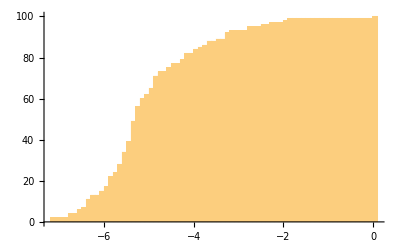

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-8.12835,0)(-7.12835,1)(-7.12835,2)(-6.78092,3)(-6.78092,4)(-6.51686,5)(-6.51686,6)(-6.42528,7)(-6.35055,8)(-6.35055,9)(-6.33666,10)(-6.33666,11)(-6.21546,12)(-6.21546,13)(-6.01958,14)(-6.01958,15)(-5.92814,16)(-5.92814,17)(-5.89003,18)(-5.89003,19)(-5.83738,20)(-5.83738,21)(-5.81284,22)(-5.72588,23)(-5.72588,24)(-5.68419,25)(-5.68419,26)(-5.67979,27)(-5.67979,28)(-5.55431,29)(-5.55431,30)(-5.5202,31)(-5.5202,32)(-5.50479,33)(-5.50479,34)(-5.49766,35)(-5.49766,36)(-5.4741,37)(-5.4741,38)(-5.45637,39)(-5.37361,40)(-5.37361,41)(-5.34394,42)(-5.34394,43)(-5.33706,44)(-5.33706,45)(-5.32616,46)(-5.32616,47)(-5.32456,48)(-5.32456,49)(-5.28751,50)(-5.2717,51)(-5.2717,52)(-5.2634,53)(-5.2634,54)(-5.21833,55)(-5.21833,56)(-5.17051,57)(-5.17051,58)(-5.16747,59)(-5.16668,60)(-5.01006,61)(-5.01006,62)(-4.92381,63)(-4.91863,64)(-4.91863,65)(-4.85034,66)(-4.85034,67)(-4.85011,68)(-4.85011,69)(-4.81318,70)(-4.81318,71)(-4.7617,72)(-4.7617,73)(-4.58771,74)(-4.58771,75)(-4.49873,76)(-4.49873,77)(-4.28422,78)(-4.28422,79)(-4.17617,80)(-4.17617,81)(-4.15077,82)(-3.9035,83)(-3.9035,84)(-3.89372,85)(-3.77606,86)(-3.67864,87)(-3.67864,88)(-3.49961,89)(-3.2559,90)(-3.2559,91)(-3.20226,92)(-3.13211,93)(-2.78312,94)(-2.78312,95)(-2.45262,96)(-2.23298,97)(-1.94691,98)(-1.8945,99)(0.,100)(0.5,100)

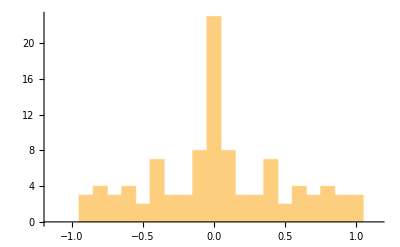

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.935589,1)(-0.928736,2)(-0.885827,3)(-0.828728,4)(-0.823686,5)(-0.813277,6)(-0.808043,7)(-0.745912,8)(-0.708374,9)(-0.692164,10)(-0.624825,11)(-0.61455,12)(-0.585293,13)(-0.564643,14)(-0.547011,15)(-0.531067,16)(-0.435581,17)(-0.430136,18)(-0.429497,19)(-0.409709,20)(-0.40255,21)(-0.375007,22)(-0.353088,23)(-0.283961,24)(-0.263385,25)(-0.255519,26)(-0.248226,27)(-0.186351,28)(-0.179213,29)(-0.133308,30)(-0.128951,31)(-0.116725,32)(-0.0961774,33)(-0.0855244,34)(-0.075293,35)(-0.075126,36)(-0.0656679,37)(-0.0372074,38)(-0.0260347,39)(-0.0211259,40)(-0.0096113,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.,56)(0.0096113,57)(0.0211259,58)(0.0260347,59)(0.0372074,60)(0.0656679,61)(0.075126,62)(0.075293,63)(0.0855244,64)(0.0961774,65)(0.116725,66)(0.128951,67)(0.133308,68)(0.179213,69)(0.186351,70)(0.248226,71)(0.255519,72)(0.263385,73)(0.283961,74)(0.353088,75)(0.375007,76)(0.40255,77)(0.409709,78)(0.429497,79)(0.430136,80)(0.435581,81)(0.531067,82)(0.547011,83)(0.564643,84)(0.585293,85)(0.61455,86)(0.624825,87)(0.692164,88)(0.708374,89)(0.745912,90)(0.808043,91)(0.813277,92)(0.823686,93)(0.828728,94)(0.885827,95)(0.928736,96)(0.935589,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Data for topic patterns

```mathematica
TopicClusters=DeleteCases[NonStopClusters,{_,_,_,"B",_,_,_,_}];
```

```mathematica
Length[TopicClusters]
```

271

```mathematica
SelectedClusters=TopicClusters;
```

```mathematica
TopicClustersBasque=TopicClusters;
```

```mathematica
Timing[PeuTopic=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{374.25,Null}

```mathematica
Timing[PeuT=Table[v=Table[prepP=PeuTopic_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,100}];v/Total[v],{m,1,100}];]
```

{0.0625,Null}

```mathematica
Timing[spec=Eigenvalues[PeuT];]
```

{1.70313,Null}

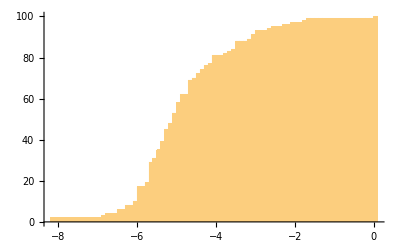

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-9.1234,0)(-8.1234,1)(-8.1234,2)(-6.84626,3)(-6.7423,4)(-6.47869,5)(-6.47869,6)(-6.25932,7)(-6.25932,8)(-6.08772,9)(-6.08772,10)(-5.96694,11)(-5.96694,12)(-5.92901,13)(-5.92901,14)(-5.91224,15)(-5.90906,16)(-5.90906,17)(-5.78221,18)(-5.78221,19)(-5.69927,20)(-5.69927,21)(-5.65361,22)(-5.65361,23)(-5.65096,24)(-5.65096,25)(-5.64676,26)(-5.64676,27)(-5.633,28)(-5.633,29)(-5.52839,30)(-5.52839,31)(-5.45904,32)(-5.45904,33)(-5.45843,34)(-5.45843,35)(-5.37547,36)(-5.37547,37)(-5.32568,38)(-5.31736,39)(-5.26618,40)(-5.26618,41)(-5.25774,42)(-5.25774,43)(-5.20021,44)(-5.20021,45)(-5.19892,46)(-5.19892,47)(-5.17381,48)(-5.08923,49)(-5.06261,50)(-5.06261,51)(-5.00607,52)(-5.00607,53)(-4.98294,54)(-4.98294,55)(-4.96046,56)(-4.96046,57)(-4.92517,58)(-4.87486,59)(-4.87486,60)(-4.87034,61)(-4.87034,62)(-4.67628,63)(-4.67628,64)(-4.66201,65)(-4.65647,66)(-4.65647,67)(-4.63247,68)(-4.63247,69)(-4.5553,70)(-4.46552,71)(-4.46552,72)(-4.37102,73)(-4.37102,74)(-4.26432,75)(-4.26432,76)(-4.17461,77)(-4.06404,78)(-4.02454,79)(-4.02454,80)(-4.00713,81)(-3.78362,82)(-3.62499,83)(-3.53276,84)(-3.48091,85)(-3.48091,86)(-3.47077,87)(-3.47077,88)(-3.15598,89)(-3.00114,90)(-3.00114,91)(-2.95109,92)(-2.95109,93)(-2.61609,94)(-2.58644,95)(-2.29295,96)(-2.05242,97)(-1.74238,98)(-1.67058,99)(0.,100)(0.5,100)

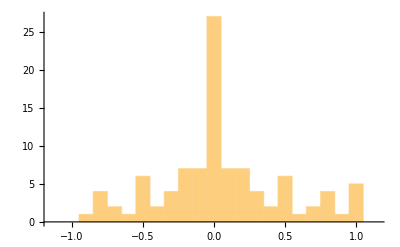

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.943019,1)(-0.82911,2)(-0.820865,3)(-0.815033,4)(-0.77909,5)(-0.710266,6)(-0.709988,7)(-0.636407,8)(-0.527647,9)(-0.478404,10)(-0.469002,11)(-0.464005,12)(-0.463654,13)(-0.45637,14)(-0.393916,15)(-0.362233,16)(-0.336614,17)(-0.321801,18)(-0.310998,19)(-0.284039,20)(-0.244221,21)(-0.233726,22)(-0.218936,23)(-0.19912,24)(-0.194131,25)(-0.175999,26)(-0.150191,27)(-0.124803,28)(-0.105978,29)(-0.099794,30)(-0.0910949,31)(-0.0831442,32)(-0.0827132,33)(-0.0563897,34)(-0.0312562,35)(-0.0291218,36)(-0.0157357,37)(-0.00669745,38)(0.,39)(0.,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.,56)(0.,57)(0.00669745,58)(0.0157357,59)(0.0291218,60)(0.0312562,61)(0.0563897,62)(0.0827132,63)(0.0831442,64)(0.0910949,65)(0.099794,66)(0.105978,67)(0.124803,68)(0.150191,69)(0.175999,70)(0.194131,71)(0.19912,72)(0.218936,73)(0.233726,74)(0.244221,75)(0.284039,76)(0.310998,77)(0.321801,78)(0.336614,79)(0.362233,80)(0.393916,81)(0.45637,82)(0.463654,83)(0.464005,84)(0.469002,85)(0.478404,86)(0.527647,87)(0.636407,88)(0.709988,89)(0.710266,90)(0.77909,91)(0.815033,92)(0.820865,93)(0.82911,94)(0.943019,95)(1.,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Word translation

#### Bulk vectors

```mathematica
EnglishRef=TopicClustersEnglish;
```

```mathematica
BasqueRef=TopicClustersBasque;
```

```mathematica
PandPChapEnglish=StringSplit[ExampleData[{"Text","PrideAndPrejudice"}],"Chapter "~~DigitCharacter..~~" "];
```

```mathematica
Length[PandPChapEnglish]
```

61

```mathematica
VecEnglish=Table[{EnglishRef_⟦k,1⟧,StringCount[PandPChapEnglish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@EnglishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[EnglishRef]}];
```

```mathematica
PandPChapBasque=StringReplace[ImportString[#,"HTML"]&/@StringReplace[StringReplace[StringReplace[StringSplit[StringReplace[Import["Pride and Prejudice (Basque).txt"],"eliz":>"ëliz"],WordCharacter..~~" "..~~"ATALA"],{"\n":>"\n舜"}],{(s:("舜"~~Repeated[Except["\n"],{1,80}]))~~"\n":>s<>"垚"}],{"舜":>""}],{"垚":>"\n\n"}];
```

```mathematica
Length[PandPChapBasque]
```

61

```mathematica
VecBasque=Table[{BasqueRef_⟦k,1⟧,StringCount[PandPChapBasque,WordBoundary~~Alternatives@@(#_⟦1⟧&/@BasqueRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[BasqueRef]}];
```

```mathematica
FlatScreenedPairs=Flatten[Table[{#_⟦1⟧,#_⟦2,k⟧},{k,1,Length[#_⟦2⟧]}]&/@Select[Table[{EnglishRef[[k,1]],#_⟦1⟧&/@Select[VecBasque,JaccardRuzickaSim[#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧]≥Max[1-7/100 √61,1-√(Length[Select[Min[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}],#>0&]]/Total[Max[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}]])]&]},{k,1,Length[EnglishRef]}],Length[#_⟦2⟧]>0&],1];
```

```mathematica
SiftedTags=Union[(#_⟦1⟧&/@FlatScreenedPairs)];SiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SiftedTags=Union[(#_⟦2⟧&/@FlatScreenedPairs)];SiftedBasqueRef=Reverse[SortBy[Table[Cases[BasqueRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
Length[SiftedEnglishRef]
```

85

```mathematica
Length[SiftedBasqueRef]
```

86

#### Spectral parameters for English

```mathematica
FromTopics=SiftedEnglishRef;
```

```mathematica
FromDelta=ReadDelta[#]&/@FromTopics;
```

```mathematica
FromN=(#_⟦3⟧-1)&/@FromTopics;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersEnglish,PenTopic,#_⟦1⟧&/@FromTopics];]
```

{58.7873,Null}

```mathematica
FromKinQ=KinQ;
```

```mathematica
FromEta=SemanticComplexities;
```

#### Spectral parameters for Basque

```mathematica
ToTopicsBasque=SiftedBasqueRef;
```

```mathematica
Length[ToTopicsBasque]
```

86

```mathematica
ToDeltaBasque=ReadDelta[#]&/@ToTopicsBasque;
```

```mathematica
ToNBasque=(#_⟦3⟧-1)&/@ToTopicsBasque;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersBasque,PeuTopic,#_⟦1⟧&/@ToTopicsBasque];]
```

{182.158,Null}

```mathematica
ToKinBasque=KinQ;
```

```mathematica
ToEtaBasque=SemanticComplexities;
```

#### Translation

```mathematica
AbsoluteTiming[fromLabeled=Transpose[{#_⟦1⟧&/@FromTopics,FromKinQ}];toLabeled=Transpose[{#_⟦1⟧&/@ToTopicsBasque,ToKinBasque}];Report=Table[{FlatScreenedPairs_⟦k⟧,(JaccardRuzickaSim[Cases[fromLabeled,{FlatScreenedPairs_⟦k,1⟧,_}]_⟦1,2⟧,Cases[toLabeled,{FlatScreenedPairs_⟦k,2⟧,_}]_⟦1,2⟧])},{k,1,Length[FlatScreenedPairs]}];]
```

{0.0144427,Null}

```mathematica
prep=Union[Select[Table[{Report_⟦n,1,1⟧,Report_⟦n,1,2⟧,Report_⟦n,2⟧},{n,1,Length[Report]}],#_⟦3⟧≥0.7&]];g=Graph[(#_⟦1⟧->#_⟦2⟧)&/@prep,EdgeWeight->(#_⟦3⟧&/@prep)];(KuhnSln={#,FindRowRank[#,prep],FindColRank[#,prep]}&/@Select[{#,PropertyValue[{g,#},EdgeWeight]}&/@FindIndependentEdgeSet[g],#_⟦2⟧>0&])//TableForm
```

{{Brighton,24}}->{{brighton,2},{brightoneko,1},{brightonen,5},{brightonera,11},{brightonerako,1},{brightonetik,4}}
0.87909992467279 | 1 | 1
{{country,40}}->{{herrari,1},{herraria,1},{herri,15},{herria,4},{herriak,1},{herrian,7},{herriarekiko,1},{herriko,4},{herrira,8},{herriren,1},{herritik,10},{herrixkaren,1},{herra,1}}
0.87864070615426 | 1 | 1
{{de,39}}->{{de,43}}
0.86743938781083 | 1 | 1
{{Bourgh,35},{Bourgh's,4}}->{{bourgh,34},{bourghek,3},{bourghi,2},{bourghen,3},{bourghengan,1}}
0.86162282142571 | 2 | 2
{{Derbyshire,24}}->{{derbyshire,3},{derbyshireko,2},{derbyshirekoan,1},{derbyshiren,9},{derbyshirera,1},{derbyshireren,4},{derbyshiretik,3},{derbyshirez,1}}
0.8492589772186 | 1 | 1
{{five,30}}->{{bosgarren,4},{bostak,2},{bostekoa,4},{bospasei,1},{bost,33},{bostetan,1}}
0.8866554896076 | 1 | 1
{{library,23}}->{{liburutegi,4},{liburutegia,3},{liburutegian,7},{liburutegiaren,1},{liburutegira,7},{liburutegitik,2}}
0.86124136880007 | 1 | 1
{{London,55}}->{{londres,2},{londreseko,7},{londresera,17},{londreseraino,2},{londreserako,1},{londresi,2},{londrestik,1},{londresen,19},{londresetik,10}}
0.85303195509879 | 1 | 1
{{Meryton,57}}->{{meryton,2},{merytoneko,10},{merytonera,13},{merytoneraino,4},{merytonerako,1},{merytonen,18},{merytonetik,8}}
0.87363103513195 | 1 | 1
{{Netherfield,73}}->{{netherfield,13},{netherfieldarrik,1},{netherfieldeko,19},{netherfieldekoak,1},{netherfieldekoek,1},{netherfieldekoen,2},{netherfielden,23},{netherfieldera,14},{netherfieldetik,7},{netherfieldi,1}}
0.85386143959241 | 1 | 1
{{oh,95}}->{{o,91}}
0.8820741642041 | 1 | 1
{{park,22}}->{{park,2},{parkean,3},{parkek,1},{parkeko,2},{parkera,1},{parkerantz,1},{parke,4},{parkeari,1},{parken,1},{parkea,2},{parkearen,3}}
0.78632033992366 | 1 | 1
{{Pemberley,53}}->{{pemberley,15},{pemberleyko,13},{pemberleykoak,1},{pemberleykoarekin,1},{pemberleyn,14},{pemberleyra,8},{pemberleyren,1},{pemberleyri,1},{pemberleytik,1},{pemberleyz,2}}
0.88288372457345 | 1 | 1
{{pounds,24}}->{{libra,20},{libre,1}}
0.86312411996734 | 1 | 1
{{Rosings,49}}->{{rosings,5},{rosingsekin,1},{rosingseko,13},{rosingsekoen,1},{rosingsen,18},{rosingsera,4},{rosingserako,2},{rosingsetik,2},{rosingsez,2},{rosingsi,1},{rosingstarrek,1}}
0.85418984041464 | 1 | 1
{{sir,78}}->{{william,29},{williamek,12},{williamen,5},{williamenak,1},{williamenean,1},{williami,2}}
0.92145998703946 | 1 | 2
{{William,40},{William's,6}}->{{sir,51}}
0.91995510772817 | 2 | 1
{{two,135}}->{{bi,80}}
0.83181086794652 | 1 | 1
{{breakfast,21},{breakfasted,1}}->{{gosari,13},{gosaria,5},{gosaritan,1},{gosaritik,1},{gosez,1},{gosal,1},{gosaldu,7},{gose,1},{gosea,1},{goserik,1}}
0.76621888460297 | 1 | 1
{{Catherine,110},{Catherine's,16}}->{{lady,171},{ladya,2},{ladyk,1},{ladyren,4},{ladyri,1}}
0.93187202559988 | 1 | 1
{{Charlotte,68},{Charlotte's,17}}->{{charlotte,37},{charlottek,35},{charlotterekiko,2},{charlotterekin,3},{charlotteren,18},{charlotterena,1},{charlotterenean,1},{charlotterengana,2},{charlotterentzat,1},{charlotteri,7}}
0.88784324378275 | 1 | 1
{{Collins,156},{Collins's,24}}->{{collins,231},{collinsek,9},{collinsen,8},{collinsi,1},{collinstarrak,3},{collinstarrei,1},{collinstarrek,1},{collinstarrekin,1}}
0.88872258421345 | 1 | 1
{{colonel,65},{colonel's,1}}->{{koronela,19},{koronelak,23},{koronelarekin,4},{koronelaren,16},{koronelarengana,2},{koronelari,8},{koronel,3}}
0.80617307501812 | 1 | 1
{{dinner,33},{dinners,2}}->{{bazkari,8},{bazkaria,7},{bazkariak,1},{bazkariaren,1},{bazkariarentzat,1},{bazkarikide,1},{bazkarira,1},{bazkaritan,1},{bazkaritara,1},{bazkaritarako,6}}
0.91840641802552 | 1 | 1
{{dine,16},{dined,8},{dines,1},{dining,6}}->{{bazkal,1},{bazkaldu,10},{bazkalduak,1},{bazkalgela,1},{bazkalgelan,1},{bazkalgelara,2},{bazkalorduan,1},{bazkalordurako,2},{bazkalostean,1},{bazkaltzearen,1},{bazkaltzeaz,1},{bazkaltzeko,10},{bazkaltzekoa,1},{bazkaltzekoak,1},{bazkaltzen,5},{bazkaltzera,8}}
0.91908901153804 | 1 | 1
{{door,32},{doors,8}}->{{atari,1},{ataritik,1},{atarramentu,2},{atartearen,1},{atartean,2},{atarterako,1},{ate,2},{ateak,1},{atean,4},{ateetako,1},{ateka,1},{ateko,3},{atetik,2},{atezainaren,1},{atea,16},{atearen,5},{ateen,1}}
0.78692859444238 | 1 | 1
{{elegance,9},{elegant,14}}->{{dotore,8},{dotorea,3},{dotoreago,2},{dotoreagorik,2},{dotoreak,2},{dotoreei,1},{dotoreen,1},{dotoreren,1},{dotoretzat,1},{dotorezia,8},{dotoreziara,1},{dotoreziaz,2}}
0.89412538802087 | 1 | 1
{{father,116},{father's,19}}->{{aita,70},{aitagatiko,1},{aitarekin,6},{aitaren,28},{aitarengana,5},{aitarenganako,1},{aitarenka,1},{aitarentzat,1},{aitatxo,3},{aitaz,1},{aitabitxi,1},{aitagana,2},{aitaginarreba,1},{aitak,42},{aitari,16},{aitarekiko,1}}
0.89407735040286 | 1 | 1
{{Fitzwilliam,32},{Fitzwilliam's,5}}->{{fitzwilliam,35},{fitzwilliamek,3}}
0.71370494298756 | 1 | 1
{{four,33},{four-and-twenty,1}}->{{lau,30}}
0.86027867353415 | 1 | 1
{{girl,38},{girls,45}}->{{neska,58},{neskak,9},{neskame,1},{neskamea,2},{neskameari,2},{neskameengana,1},{neskarekin,3},{neskaren,8},{neskarengana,2},{neskarik,2},{neskatila,2},{neskatilak,6},{neskatilaren,2},{neskatilari,1},{neskatilei,1},{neskatilek,4},{neskatilen,1},{neskatiletako,2},{neskatiletakoren,1},{neskatoren,1},{neskatxa,1},{neskatxei,1},{neskaz,1},{neskazahar,1},{neskazaharra,1},{nesketako,2},{nesketakoren,1},{neskok,3},{neskek,2},{neskez,1},{neskei,4},{nesken,2},{neskentzat,2}}
0.86300826937502 | 1 | 1
{{Jane,263},{Jane's,28}}->{{jane,113},{janek,122},{janerekiko,5},{janerekin,11},{janeren,58},{janerena,3},{janerengan,1},{janerengana,2},{janerenganako,1},{janerengandik,1},{janerengatik,2},{janerentzat,3},{janeri,39},{janerik,1},{janez,4}}
0.90585994154463 | 1 | 1
{{Kitty,69},{Kitty's,2}}->{{kitatu,2},{kito,3},{kitty,40},{kittyk,22},{kittyrekin,1},{kittyren,3},{kittyrena,1},{kittyrengatik,1},{kittyrentzat,3},{kittyri,4},{kitagarri,1}}
0.93108525111276 | 1 | 1
{{Lizzy,95},{Lizzy's,2}}->{{lizzy,87},{lizzyrekin,3},{lizzyren,2},{lizzyz,1},{lizzyk,5},{lizzyri,3}}
0.931678686589 | 1 | 1
{{Lydia,133},{Lydia's,38}}->{{lydia,89},{lydiagatik,1},{lydiarekin,12},{lydiaren,37},{lydiarenak,1},{lydiarengan,1},{lydiarengana,1},{lydiarengandik,1},{lydiarentzat,3},{lydiak,67},{lydiari,21}}
0.90688338837148 | 1 | 1
{{Mary,38},{Mary's,1}}->{{mary,18},{maryren,1},{marytonen,1},{maryk,20},{maryri,2}}
0.75501402727344 | 1 | 1
{{room,112},{rooms,8}}->{{geldi,3},{gela,36},{gelako,9},{gelan,42},{gelara,24},{gelaz,1},{gelak,5},{gelari,1}}
0.84738301535858 | 1 | 1
{{serious,24},{seriously,13}}->{{serio,18},{serioa,2},{serioago,1},{serioagoan,1},{serioaz,1},{serioenean,1},{serioko,1},{serioski,1},{seriotasun,2},{seriotasuna,2},{seriotasunari,1}}
0.87863176661433 | 1 | 1
{{table,28},{tables,3}}->{{mahai,10},{mahaia,6},{mahaiak,5},{mahaian,7},{mahaiaren,3},{mahaiburu,1},{mahaiburuan,1},{mahaikoen,1},{mahaira,3},{mahairantz,1},{mahaitik,2},{mahats,1},{mahuka,1}}
0.9048781112577 | 1 | 1
{{ten,33},{tens,1}}->{{hamar,39}}
0.76105591209702 | 1 | 1
{{way,108},{ways,3}}->{{alda,1},{aldabera,1},{aldaberak,1},{aldaberakoa,1},{aldaezin,1},{aldaezinak,1},{aldagaitzaren,1},{aldaketa,16},{aldaketak,2},{aldaketaren,3},{aldaketari,1},{aldaketarik,3},{aldaketaz,1},{aldakor,1},{aldamenean,3},{aldatu,21},{aldatua,1},{aldatuko,11},{aldatuta,5},{aldatutakoan,1},{aldatuz,1},{aldatze,2},{aldatzea,6},{aldatzeak,2},{aldatzeaz,1},{aldatzeko,2},{aldatzen,7},{aldaerrazak,1},{aldapan,1},{aldarera,1},{aldarte,7},{aldarterik,1},{aldartean,1}}
0.8291564655098 | 1 | 1
{{week,29},{weeks,18}}->{{aste,22},{asteak,1},{astean,9},{asteartean,9},{asteartera,3},{asteetan,1},{astelehen,1},{astelehena,1},{astelehenarekin,3},{astelehenean,2},{astelehenera,1},{astera,1},{astea,2},{astearen,1},{asteazken,1},{asteazkenean,5},{asteazkeneko,1},{asteazkenerako,1},{asteazkenetik,1},{astebete,7},{astebetea,1},{astebetera,2},{astebeterako,1},{astebetez,1},{asteen,1}}
0.91993527890215 | 1 | 1
{{window,16},{windows,6}}->{{leiho,8},{leihoa,1},{leihoak,2},{leihoaren,2},{leihoen,1},{leihora,1},{leihorantz,2},{leihotik,4}}
0.92912431864058 | 1 | 1
{{aunt,78},{aunt's,6},{aunts,1}}->{{izeko,50},{izekoak,19},{izekoari,3},{izeba,3},{izebarekin,1},{izebaren,1},{izebarenganako,1},{izekoa,5},{izekoarekin,4},{izekoaren,7},{izekoarena,1},{izekoarenera,1},{izekoarengana,1},{izekoarengandik,1},{izekok,5},{izekori,1},{izekorik,1}}
0.876444256839 | 1 | 1
{{Bennet,294},{Bennet's,29},{Bennets,10}}->{{bennet,447},{bennetar,2},{bennetarrak,5},{bennetarrei,1},{bennetarrek,1},{bennetarrekiko,1},{bennetarrekin,1},{bennetarren,3},{bennetek,4}}
0.90643758842148 | 1 | 1
{{book,16},{books,13},{book-room,1}}->{{liburu,19},{liburuak,5},{liburuan,2},{liburuari,1},{liburuek,1},{liburuetatik,1},{liburuez,2},{liburuko,1},{liburuok,1},{liburutik,1},{liburua,7},{liburuaren,1}}
0.81002478320876 | 1 | 1
{{cousin,41},{cousin's,8},{cousins,11}}->{{lehengusina,20},{lehengusinak,6},{lehengusinarekin,1},{lehengusinaren,5},{lehengusinarentzako,1},{lehengusinari,4},{lehengusinei,2},{lehengusinekin,2},{lehengusinen,1},{lehengusu,3},{lehengusua,13},{lehengusuak,21},{lehengusuarekiko,2},{lehengusuaren,16},{lehengusuari,2},{lehengusuaz,1}}
0.90669344378224 | 1 | 1
{{dear,158},{dearly,3},{dearest,17}}->{{ene,118},{eneak,2},{enean,5},{eneari,2},{eneko,2},{enekoak,1},{enera,1},{enetik,1},{enea,1}}
0.88511023569514 | 1 | 1
{{Forster,38},{Forster's,1},{Forsters,1}}->{{forster,41},{forstertarrek,1}}
0.92673083839173 | 1 | 1
{{Gardiner,84},{Gardiner's,13},{Gardiners,6}}->{{gardiner,108},{gardinertar,1},{gardinertarrak,3},{gardinertarrei,1},{gardinertarrek,2},{gardinertarrekin,1},{gardinerrek,2},{gardinerri,1}}
0.89768192088985 | 1 | 1
{{Hurst,32},{Hurst's,1},{Hursts,1}}->{{hurst,36},{hurstarrek,1}}
0.70633007036153 | 1 | 1
{{husband,42},{husband's,8},{husbands,4}}->{{senarrak,12},{senarrarekikoak,1},{senarrari,8},{senarra,20},{senarrarekin,3},{senarraren,7},{senarrarena,1},{senarrarengana,1}}
0.89070659941254 | 1 | 1
{{interest,26},{interested,8},{interesting,14}}->{{interesa,1},{interesak,3},{interesaren,1},{interes,2},{interesatu,1},{interesatua,1},{interesatuen,1},{interesaturik,1},{interesatzen,1},{interesetan,1},{interesgarri,4},{interesgarria,2},{interesgarriago,4},{interesgarriagoak,1},{interesgarriegiak,1},{interesgarrien,1},{interesik,1},{interesen,2},{interpretatu,1},{interpretazio,1}}
0.7923482454368 | 1 | 1
{{Phillip's,1},{Phillips,26},{Phillips's,5}}->{{philips,34},{philipsek,3},{philipsi,2},{philipstarrak,3},{philipstarrekin,1},{philipstarren,1}}
0.91358572586444 | 1 | 1
{{sat,38},{sit,15},{sitting,20}}->{{jesar,2},{jesarlekutik,1},{jesarrarazi,1},{jesarri,17},{jesarriko,1},{jesarrita,22},{jesartzea,2},{jesartzearekin,1},{jesartzeko,3},{jesartzen,5},{jesartzera,2}}
0.89575445229304 | 1 | 1
{{year,28},{years,33},{years',2}}->{{urtaro,1},{urtarrila,1},{urtarrilean,1},{urte,42},{urteak,1},{urtean,14},{urteetako,3},{urteetan,3},{urteetara,1},{urteetatik,2},{urteko,8},{urteon,1},{urterekin,2},{urtero,6},{urtez,1},{urtebete,5},{urtebeteko,1},{urtebetez,2},{urterik,1}}
0.90830674873101 | 1 | 1
{{young,130},{younger,30},{youngest,13}}->{{gazte,81},{gaztea,23},{gazteei,5},{gazteoi,1}}
0.75649747880519 | 1 | 1
{{attach,3},{attached,11},{attachment,27},{attachments,1}}->{{atxiki,2},{atxikia,3},{atxikiko,2},{atxikimendu,11},{atxikimendua,8},{atxikimenduak,3},{atxikimenduaren,3},{atxikimenduaz,2},{atxikimendurik,1},{atxikirik,2},{atxikita,2},{atxikitzeko,1},{atxikitzen,1}}
0.84104979306214 | 1 | 1
{{best,41},{better,92},{good,184},{good-humoured,6}}->{{hobe,24},{hobea,14},{hobeak,4},{hobean,1},{hobearen,1},{hobeek,1},{hobekien,1},{hobekorik,1},{hobekuntza,1},{hobekuntzak,1},{hoben,1},{hobendun,3},{hobera,4},{hoberanzkoa,1},{hoberen,1},{hoberenak,1},{hoberenen,1},{hoberentzat,1},{hoberik,8},{hobeto,41},{hobetoen,2},{hobetotxo,1},{hobetu,5},{hobetuko,1},{hobetuta,1},{hobetuz,1},{hobetxoan,1},{hobetzeko,1},{on,33},{ona,93},{onak,35},{onean,14},{onei,1},{oneko,14},{onekoa,9},{onekoak,1},{onen,3},{onena,14},{onenak,7},{onenarekin,1},{onenaren,2},{onenean,6},{onenetako,2},{onenetan,3},{onera,6},{onerako,6},{onestasuna,1},{onetik,4},{onez,28},{onezko,1},{onik,23}}
0.72869447996381 | 1 | 1
{{Bingley,257},{Bingley's,49},{Bingleys,4},{Bingleys',1}}->{{bingley,346},{bingleyrekin,1},{bingleyren,30},{bingleyrena,1},{bingleyrengan,1},{bingleyrengana,3},{bingleyrengatik,1},{bingleytarrak,1},{bingleytarrekin,1},{bingleytarren,2},{bingleyganako,1},{bingleyk,43},{bingleyri,16},{bingleyrekiko,2}}
0.8370189542742 | 1 | 1
{{brother,62},{brotherly,2},{brother's,13},{brothers,2}}->{{anaiak,1},{anaiari,5},{nebak,11},{nebarekiko,1},{nebari,8},{nebarik,2},{anaia,4},{anaiarengana,1},{neba,35},{nebarekin,1},{nebaren,16},{nebarenak,1},{nebarengandik,1},{nebarentzat,1},{nebaz,1}}
0.92329736870605 | 1 | 1
{{came,90},{come,93},{comes,16},{coming,61}}->{{badator,4},{badatorkizu,1},{bazetorren,1},{bazetorrena,1},{betozkoa,1},{dator,4},{datorkigu,2},{datorkigunean,1},{datorkiola,2},{datorkion,1},{datorrela,4},{datorren,6},{datorrena,1},{datorrenean,2},{datoz,1},{datozen,3},{etor,6},{etorbide,1},{etorbidera,1},{etorkizun,6},{etorkizunaren,1},{etorkizunari,2},{etorkizunaz,1},{etorkizunean,4},{etorkizuneko,5},{etorkor,3},{etorrarazi,1},{etorrera,3},{etorrerak,5},{etorrerako,1},{etorreraren,4},{etorreraz,2},{etorri,123},{etorria,18},{etorriak,3},{etorriaz,1},{etorriko,35},{etorririk,2},{etorririko,1},{etorrita,4},{etorritako,5},{etortze,1},{etortzea,13},{etortzeagatik,2},{etortzeak,4},{etortzean,1},{etortzearen,1},{etortzeko,15},{etortzekoa,4},{etortzekoak,2},{etortzen,19},{etortzera,3},{etortzerik,1},{gatozen,1},{gatozenean,1},{nator,1},{natorkizu,1},{zatoz,3},{zatozenean,1},{zatoztenean,1},{zetorkion,1},{zetorrela,9},{zetorren,10},{zetorrena,2},{zetozela,3},{zetozen,6},{zetozkien,1},{zetozkion,1}}
0.91444879319775 | 1 | 1
{{character,64},{characters,3},{characterise,1},{characteristic,2}}->{{izaera,39},{izaeragatik,1},{izaerak,8},{izaeran,1},{izaerarekin,3},{izaeraren,6},{izaerari,6},{izaeratik,1},{izaeraz,8},{izaki,3},{izakia,1},{izakirik,4},{izaerekin,1},{izaeren,2},{izaeretan,1}}
0.73125395744308 | 1 | 1
{{daily,3},{day,130},{day's,4},{days,30}}->{{egun,79},{eguna,19},{egunak,5},{egunaren,5},{egunari,1},{egunaz,1},{egundo,5},{egundoko,2},{egundokoak,1},{egunean,22},{eguneko,4},{egunen,11},{egunera,9},{egunero,15},{eguneroko,6},{egunetan,4},{egunetara,1},{egunetik,2},{egunez,4},{egunik,3},{egunkari,1},{egunkarietan,1},{egunotan,1},{eguerdi,2},{eguerdirako,1},{eguraldi,4},{eguraldia,2}}
0.90880422548429 | 1 | 1
{{honour,42},{honoured,9},{honours,2},{honourable,6}}->{{oholesi,1},{oholesia,2},{ohoragarriaz,1},{ohoratuko,1},{ohoratzen,2},{ohoretan,1},{ohorezko,2},{ohorezkoan,1},{ohore,7},{ohoreak,5},{ohoreari,1},{ohoredun,2},{ohoretsu,2},{ohoretsua,1},{ohoretsuak,2},{ohoretsuenean,1},{ohorea,26},{ohoreagatik,1},{ohorearen,3},{ohoreaz,1},{ohorerik,1}}
0.87098251096253 | 1 | 1
{{Lucas,65},{Lucas's,5},{Lucases,13},{Lucases',1}}->{{lucasi,9},{lucastar,3},{lucastarrak,4},{lucastarrek,1},{lucastarrekin,1},{lucastarren,3},{lucastarrenean,1},{lucas,53},{lucasek,7},{lucasena,1},{lucasterrek,1},{lucasekin,2},{lucasen,1},{lucasenekora,2},{lucasengana,1}}
0.85476595716534 | 1 | 1
{{promise,17},{promised,21},{promises,3},{promising,4}}->{{agi,1},{agindu,23},{agindua,9},{aginduak,8},{aginduez,1},{aginduidazu,1},{aginduka,1},{aginduko,3},{agindupean,1},{aginduta,1},{agindutako,3},{agindutakoa,1},{agindutakoari,2},{aginduz,2},{aginduzkoan,1},{aginpide,1},{agintea,1},{aginteaz,1},{agintzaileetatik,1},{agintzen,3},{agitu,1},{agitzen,1}}
0.85610127199463 | 1 | 1
{{send,24},{sending,1},{sends,1},{sent,20}}->{{bidal,3},{bidali,19},{bidalia,2},{bidaltzea,3}}
0.85828378367257 | 1 | 1
{{carriage,44},{carriages,6},{carried,8},{carry,5},{carrying,4}}->{{kotxe,12},{kotxea,31}}
0.83012356648834 | 1 | 1
{{console,9},{consoled,2},{consoling,3},{consolation,10},{consolatory,1}}->{{kontsolatu,2},{kontsolatzen,3},{kontsola,2},{kontsolabide,6},{kontsolabidea,1},{kontsolabiderik,1},{kontsolagarria,1},{kontsolamendu,3},{kontsolamendua,3},{kontsolamenduaz,1},{kontsolamendurako,1},{kontsolamendurik,1}}
0.87659783034809 | 1 | 1
{{invite,6},{invited,11},{inviting,3},{invitation,34},{invitations,1}}->{{gona,4},{gonbidapen,5},{gonbidapena,11},{gonbidapenak,1},{gonbidapenaren,1},{gonbidapenean,1},{gonbidapenik,6},{gonbidatu,12},{gonbidatua,4},{gonbidatuarekin,1},{gonbidatuei,1},{gonbidatuen,1},{gonbidatuenganako,1},{gonbidatuko,1},{gonbidaturik,1},{gonbidatuta,3},{gonbidatzea,2},{gonbidatzeko,9},{gonbidatzen,2},{gonbidatzeraino,1},{gonbit,2},{gonbita,9},{gonbitari,1},{gonbitetan,1},{gonbitik,1}}
0.9128466555162 | 1 | 1
{{knew,58},{know,238},{knowing,27},{known,57},{knows,9}}->{{badaki,5},{badakigu,1},{badakigunez,1},{badakit,22},{badakizu,30},{badakizue,2},{banekielako,2},{banekien,9},{bazekiela,1},{bazekien,11},{bazekienez,1},{bazekiten,1},{daki,8},{dakidala,1},{dakidalako,1},{dakidanez,1},{dakielako,1},{dakienean,2},{dakienik,1},{dakigu,4},{dakigunez,1},{dakiokeen,1},{dakit,41},{dakite,2},{dakizki,1},{dakizu,13},{dakizue,1},{dakizunean,1},{jaki,6},{jakin,111},{jakina,31},{jakinarazi,18},{jakinarazia,2},{jakinaraziko,1},{jakinaraziozu,1},{jakinaraziz,1},{jakinarazpen,2},{jakinarazpena,1},{jakinaraztea,2},{jakinaraztearen,1},{jakinarazteaz,1},{jakinarazteko,5},{jakinarazten,4},{jakinaren,7},{jakinarena,1},{jakinda,3},{jakineko,1},{jakinen,1},{jakinez,1},{jakineza,1},{jakinezaren,1},{jakingai,1},{jakingarri,1},{jakingo,10},{jakingura,6},{jakingurari,1},{jakingurarik,1},{jakinik,4},{jakintsu,1},{jakintsuenak,1},{jakiren,2},{jakitea,17},{jakiteagatik,2},{jakiteak,5},{jakitean,4},{jakitearen,2},{jakitegiek,1},{jakiteko,25},{jakiten,1},{jakitera,2},{jakiterik,1},{jakitun,15},{jakituria,1},{jakituriaz,1},{nekien,5},{nekienaren,1},{zekiela,2},{zekienez,3},{zekienik,1},{zekiokeena,1},{zekitela,1},{zekiten,2},{zekitena,1}}
0.75205516954085 | 1 | 1
{{master,25},{masterly,1},{master's,3},{masters,2},{mistress,9}}->{{ugazaba,31},{ugazabaren,2},{ugazabarik,1},{ugaltzen,1}}
0.73548487159737 | 1 | 1
{{miss,283},{missed,3},{missing,1},{missent,2},{missish,1}}->{{andereño,36},{andereñoa,125},{andereñoagana,1},{andereñoak,120},{andereñoarekiko,5},{andereñoarekin,12},{andereñoaren,40},{andereñoarena,3},{andereñoarenera,1},{andereñoarengan,1},{andereñoarengana,7},{andereñoarenganako,1},{andereñoarengatik,1},{andereñoarentzako,1},{andereñoarentzat,2},{andereñoari,29},{andereñoaz,2},{andereñoei,1},{andereñoek,6},{andereñoen,1},{andereñoren,1},{andereñorik,4}}
0.70238078069484 | 1 | 1
{{pride,47},{prided,1},{proud,22},{proudly,1},{proudest,1}}->{{harro,21},{harroa,11},{harroago,1},{harroak,1},{harroegia,1},{harrokeria,2},{harrokeriak,2},{harrokeriaren,1},{harrokeriari,3},{harrokeriaz,1},{harrokeriazko,1},{harroputzaren,1},{harropuzkeria,1},{harropuzkeriari,1},{harrotasun,8},{harrotasuna,18},{harrotasunak,6},{harrotasunaren,2},{harrotasunarentzat,1},{harrotasunari,2},{harrotasunean,1},{harrotasunetik,1},{harrotasunez,2},{harrotu,5},{harrotuko,1},{harroturik,1},{harrotzat,1},{harrotzeak,1},{harrotzeko,1},{harroxko,1},{harroxkotasun,1},{harroxkotasuna,1}}
0.87102590400981 | 1 | 1
{{saw,103},{see,149},{seeing,60},{seen,76},{sees,6}}->{{ikusaraztea,1},{ikus,8},{ikusaraziz,1},{ikusgai,2},{ikusgarritasuna,1},{ikusi,226},{ikusia,10},{ikusiaz,1},{ikusiko,25},{ikusirik,4},{ikusita,37},{ikusitako,5},{ikusitakoa,1},{ikusitakoak,3},{ikusitakoarekin,1},{ikusitakoekin,1},{ikusitakotik,1},{ikusiten,1},{ikusiz,5},{ikuskaria,1},{ikuskatu,1},{ikuskerarekin,1},{ikuskizun,1},{ikusle,1},{ikuspegi,7},{ikuspegia,3},{ikuspegiak,1},{ikuspegiaz,1},{ikustaldi,2},{ikustaldia,2},{ikustaldiak,2},{ikuste,1},{ikustea,17},{ikusteagatik,2},{ikusteak,9},{ikustearekin,1},{ikustearen,2},{ikustearena,1},{ikusteari,1},{ikusteaz,11},{ikusteko,67},{ikusten,76},{ikusmirak,1},{ikusmiran,1},{ikusmiratik,1},{ikustean,14},{ikustera,1}}
0.76351489535354 | 1 | 1
{{forget,17},{forgetfulness,1},{forgets,1},{forgetting,2},{forgot,5},{forgotten,12}}->{{ahaztarazi,2},{ahaztea,1},{ahazteko,3},{ahaztu,19},{ahaztua,3},{ahaztuko,6},{ahaztuta,2},{ahaztera,3}}
0.71368339846632 | 1 | 1
{{marriage,66},{married,61},{marry,42},{marrying,23},{matrimonial,1},{matrimony,6}}->{{ezko,1},{ezkon,9},{ezkonarazi,1},{ezkonaraztea,1},{ezkonberri,1},{ezkonberriak,1},{ezkonberriek,1},{ezkonberrien,1},{ezkonberritasuna,1},{ezkonbidean,1},{ezkonbizitza,1},{ezkonbizitzako,1},{ezkonbizitzan,1},{ezkonbizitzaren,1},{ezkondu,41},{ezkondua,3},{ezkonduek,1},{ezkonduko,13},{ezkonduta,17},{ezkonduz,1},{ezkongai,3},{ezkontarazi,1},{ezkontidearekiko,1},{ezkontza,53},{ezkontzak,6},{ezkontzan,3},{ezkontzara,3},{ezkontzarako,6},{ezkontzarekin,5},{ezkontzaren,10},{ezkontzarena,3},{ezkontzarenak,1},{ezkontzari,1},{ezkontzatik,1},{ezkontzaz,3},{ezkontzea,19},{ezkontzeak,4},{ezkontzearen,3},{ezkontzeari,2},{ezkontzeaz,1},{ezkontzeko,20},{ezkontzekorik,1},{ezkontzekotan,3},{ezkontzen,5},{ezkontzera,5},{ezkontzerakoan,1}}
0.94320601245889 | 1 | 1
{{visit,51},{visited,4},{visiting,5},{visits,5},{visitor,11},{visitors,14}}->{{bisitak,2},{bisitaldi,3},{bisitaldia,4},{bisitaldiak,1},{bisitaldian,2},{bisitaldiaren,3},{bisitaldiko,1},{bisitan,24},{bisitari,9},{bisitaria,7},{bisitariak,9},{bisitariaren,1},{bisitariei,1},{bisitariekin,1},{bisitarientzat,1},{bisitatu,1},{bisitatuko,1},{bisitatzeko,2},{bisitatzen,3},{bisita,26},{bisitaka,1},{bisitaren,2},{bisitatik,2},{bisitaz,1},{bisitengatik,1}}
0.94465684186238 | 1 | 1
{{write,39},{writes,1},{writing,12},{written,19},{writer,3},{wrote,21}}->{{idatz,2},{idatzi,49},{idatzia,5},{idatziak,2},{idatzidazu,1},{idatziko,5},{idatzita,1},{idatzitako,2},{idazkaria,1},{idazkera,2},{idazkeragatik,1},{idazkeran,1},{idazkeratik,1},{idazketa,1},{idazleak,1},{idazmahaitik,1},{idaztea,3},{idaztean,2},{idazteari,3},{idazteko,4},{idazten,18},{idaztera,1},{idazterakoan,1},{ideiez,1}}
0.90890932161317 | 1 | 1
{{like,77},{liked,27},{likely,38},{likeness,3},{likes,9},{liking,2},{likelihood,5}}->{{entzule,4},{entzuleetariko,1},{entzuleria,1},{entzun,110},{entzuna,3},{entzunarena,2},{entzunbide,1},{entzunda,10},{entzundako,3},{entzundakoa,1},{entzundakoagatik,1},{entzundakoaz,1},{entzungarrian,1},{entzungo,10},{entzungor,2},{entzunik,1},{entzutea,6},{entzuteak,5},{entzutearen,1},{entzuteaz,1},{entzuteko,22},{entzuten,24},{entzuterik,1},{entzutean,9},{entzutera,5}}
0.794281754219 | 1 | 1
{{gentle,5},{gentleness,4},{gentlemen,34},{gentlemen's,3},{gentleman,32},{gentleman's,8},{gentlemanlike,8},{gentlest,1},{gentlewoman,1}}->{{zaldun,37},{zaldunago,1},{zaldunak,20},{zaldunari,2},{zaldunek,2},{zaldunetako,1},{zaldunetakoren,1},{zalduni,1},{zalduna,5},{zaldunarekin,1},{zaldunaren,3},{zaldunekin,1}}
0.74009165198016 | 1 | 1

```mathematica
ResiftedTags=Union[(#_⟦1⟧&/@prep)];ResiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
ResiftedTags=Union[(#_⟦2⟧&/@prep)];ResiftedBasqueRef=Reverse[SortBy[Table[Cases[BasqueRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SemanticSim={Position[ResiftedEnglishRef,{#_⟦1⟧,___}]_⟦1,1⟧,Position[ResiftedBasqueRef,{#_⟦2⟧,___}]_⟦1,1⟧,#_⟦3⟧}&/@prep;
```

```mathematica
OptimalNodes={Position[ResiftedEnglishRef,{#_⟦1,1,1⟧,___}]_⟦1,1⟧,Position[ResiftedBasqueRef,{#_⟦1,1,2⟧,___}]_⟦1,1⟧,#_⟦2,1,1⟧,#_⟦3,1,1⟧}&/@KuhnSln;
```

```mathematica
Export["PnP_EnglishBasque.txt","%tournament\n"<>StringJoin[Riffle[Flatten["\\put("<>ToString[1.5+1+4#_⟦2⟧]<>","<>ToString[90-4#_⟦1⟧]<>"){\\color[rgb]"<>ToString[TempRGB[#_⟦3⟧]]<>"{\\rule{4pt}{4pt}}}"&/@SemanticSim],"\n"]]<>"\n%crosshairs\n"<>StringJoin[Riffle["\n%"<>ResiftedEnglishRef[[#_⟦1⟧,1,1,1]]<>"_"<>ResiftedBasqueRef[[#_⟦2⟧,1,1,1]]<>"
\\put("<>ToString[1.5+4#_⟦2⟧+3]<>","<>ToString[90-4#_⟦1⟧+2]<>"){\\color{green}\\linethickness{"<>ToString[1.5/#_⟦3⟧]<>"pt}\\line(-1,0){"<>ToString[4#_⟦2⟧-2]<>"}\\linethickness{"<>ToString[1.5/#_⟦4⟧]<>"pt}\\line(0,1){"<>ToString[4#_⟦1⟧-2]<>"}}"&/@OptimalNodes,"\n"]]];
```

#### English labels

```mathematica
FromClusters=ResiftedEnglishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
EnglishCompress[w_]:=StringReplace[w,{"ai":>"𝔸","ea":>"𝕀","ou":>"𝕌","ee":>"𝔼","oo":>"𝕆"}]
```

```mathematica
EnglishDecompress[w_]:=StringReplace[w,{"𝔸":>"ai","𝕀":>"ea","𝕌":>"ou","𝔼":>"ee","𝕆":>"oo"}]
```

```mathematica
EvenOut[cl_]:=(prep=EnglishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,EnglishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["EnglishLabels_for_Basque_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5-3Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[91.75-1.5-4k]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]]
```

EnglishLabels_for_Basque_PnP.txt

#### Basque labels

```mathematica
FromClusters=ResiftedBasqueRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
BasqueSort[WordFreqList_]:=Transpose[(assoc=<|#_⟦1⟧->#_⟦2⟧&/@Transpose[WordFreqList]|>;{#,assoc[#]}&/@AlphabeticSort[Keys[assoc],"Spanish"])]
```

```mathematica
BasqueCompress[w_]:=StringReplace[w,{}]
```

```mathematica
BasqueDecompress[w_]:=StringReplace[w,{}]
```

```mathematica
RemoveExtraSpace[cl_]:=(sp=Max[0,Min[First[#]_⟦1⟧&/@StringPosition[Transpose[cl]_⟦1⟧,Except[" "],1]-1]];Table[{StringDrop[cl_⟦n,1⟧,sp],cl_⟦n,2⟧},{n,1,Length[cl]}])
```

```mathematica
ClusterCount={{"badaki","daki","jaki"},{10,72,83}}
```

{{badaki,daki,jaki},{10,72,83}}

```mathematica
PadPrefix0[cl_]:=(HeuristicPrefixL=(Max[#]-1)&/@((Last[#]&/@StringPosition[#,WordBoundary~~"ba"|"be"|"i"|"zi"|"e"|"da"|"na"|"za"|"ze"|"zen"|""~~LetterCharacter,Overlaps->All])&/@cl_⟦1⟧);MaxPrefixL=Max[HeuristicPrefixL];{Table[{StringDrop[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],StringPadLeft[StringTake[cl_⟦1,n⟧,HeuristicPrefixL_⟦n⟧],MaxPrefixL," "]},{n,1,Length[cl_⟦1⟧]}],cl_⟦2⟧})
```

```mathematica
PadPrefix[cl_]:=BasqueSort[RefString=Last[SortBy[#_⟦1⟧&/@cl_⟦1⟧,StringLength[#]&]];Transpose[Table[prep=SequenceAlignment[RefString,cl_⟦1,n,1⟧];If[Length[prep_⟦1⟧]>1,Lmax=Max[StringLength/@prep_⟦1⟧];{Table[" ",{m,1,Lmax-StringLength[prep_⟦1,2⟧]}]<>cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧},{cl_⟦1,n,2⟧<>cl_⟦1,n,1⟧,cl_⟦2,n⟧}],{n,1,Length[cl_⟦1⟧]}]]]
```

```mathematica
EvenOut[cl_]:=(prep0=PadPrefix[PadPrefix0[cl]];prep=BasqueCompress[prep0_⟦1⟧];L=Max[StringLength[prep]];RemoveExtraSpace[{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,prep0_⟦2⟧}]])
```

```mathematica
EvenOut[ClusterCount]
```

{{  daki,72},{  jaki,83},{badaki,10}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,BasqueDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
 
72 | 2
 
72 | 3
d
72 | 4
a
72 | 5
k
72 | 6
i
72
1
 
83 | 2
 
83 | 3
j
83 | 4
a
83 | 5
k
83 | 6
i
83
1
b
10 | 2
a
10 | 3
d
10 | 4
a
10 | 5
k
10 | 6
i
10

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{6,i,72},{6,i,83},{6,i,10}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
 
72 | 1
 
83 | 1
b
10
2
 
72 | 2
 
83 | 2
a
10
3
d
72 | 3
j
83 | 3
d
10
4
aki
165 |  |

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
b
10 | 1
 
155 | 
2
a
10 | 2
 
155 | 
3
d
10 | 3
j
83 | 3
d
72
4
aki
165 |  |

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["BasqueLabels_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5.25-.25+1+4k]<>","<>ToString[91]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BCR{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=StringReplace[ToUpperCase[StringReplace[BCData_⟦m,n,2⟧,{"ß":>"𝕊"}]],"𝕊":>"ß"];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Ç":>"C"}];RemoveDiacritics[temp1,Language->"English"]==temp1,1,1.4],10^-3]]])<>"}{"<>temp<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

```mathematica
Export["EnglishBasque_Report.txt",{Last[SortBy[#_⟦1,1,1⟧,Last]]_⟦1⟧,Last[SortBy[#_⟦1,1,2⟧,Last]]_⟦1⟧}&/@KuhnSln];
```